```mathematica
Directory[]
```

/home/marvin/Nutstore/Store/github/WhyMathematica/DataVisualization/Other/MarriageableAge

## Marriageable Age of Different Countries

Data Import

```mathematica
dataXLS=Import["Data/rawData.xls","XLS"];
```

```mathematica
Grid[ToExpression[dataXLS[[1]]]]
```

苏丹 | 青春期 | 青春期
尼日尔 | 15. | 15.
肯尼亚 | 16. | 16.
坦桑尼亚 | 18. | 15.
索马里 | 18. | 16.
津巴布韦 | 18. | 16.
马达加斯加 | 18. | 17.
埃及 | 18. | 18.
埃塞俄比亚 | 18. | 18.
马里 | 18 或15 | 18 或15
摩洛哥 | 18. | 18.
尼日利亚 | 18. | 18.
南非 | 18. | 18.
南苏丹 | 18. | 18.
塞内加尔 | 20. | 16.
突尼斯 | 20. | 17.
利比亚 | 20. | 20.
阿尔及利亚 | 21. | 18.
阿富汗 | 18. | 16.
亚美尼亚 | 18. | 17.
阿塞拜疆 | 18. | 17.
孟加拉国 | 21. | 18.
文莱 | 没有规定最低结婚年龄 | 
中华人民共和国 | 22. | 20.
格鲁吉亚 | 18. | 18.
香港 | 21. | 21.
印度 | 21. | 18.
印尼 | 19. | 16.
伊朗 | 18. | 16.
伊拉克 | 18. | 18.
以色列 | 18. | 17.
日本 | 20. | 20.
约旦 | 16. | 15.
哈萨克斯坦 | 18. | 18.
韩国 | 18. | 18.
科威特 | 没有规定最低结婚年龄 | 
吉尔吉斯斯坦 | 18. | 18.
黎巴嫩 | 18. | 17.
马来西亚 | 21. | 21.
马尔代夫 | 15. | 15.
尼泊尔 | 21. | 18.
巴基斯坦 | 18. | 16.
巴勒斯坦国 | 16. | 15.
蒙古国 | 18. | 18.
菲律宾 | 18. | 18.
俄罗斯 | 18. | 18.
沙特阿拉伯 | 未定 | 
新加坡 | 21. | 21.
斯里兰卡 | 18. | 18.
叙利亚 | 18. | 17.
中华民国 | 18. | 16.
泰国 | 17. | 17.
土耳其 | 18. | 18.
乌兹别克斯坦 | 18. | 17.
越南 | 20. | 18.
也门 | 未定 | 
阿尔巴尼亚 | 18. | 16.
亚美尼亚 | 18. | 17.
奥地利 | 18. | 18.
阿塞拜疆 | 18. | 17.
白俄罗斯 | 18. | 18.
比利时 | 18. | 18.
保加利亚 | 18. | 18.
克罗地亚 | 18. | 18.
塞浦路斯 | 18. | 18.
捷克 | 18. | 18.
丹麦 | 18. | 18.
爱沙尼亚 | 18. | 18.
芬兰 | 18. | 18.
法国 | 18. | 18.
格鲁吉亚 | 18. | 18.
德国 | 18. | 18.
直布罗陀 | 18. | 18.
希腊 | 18. | 18.
匈牙利 | 18. | 18.
冰岛 | 18. | 18.
爱尔兰共和国 | 18. | 18.
意大利 | 18. | 18.
拉脱维亚 | 18. | 18.
立陶宛 | 18. | 18.
荷兰 | 18. | 18.
挪威 | 18. | 18.
波兰 | 18. | 18.
葡萄牙 | 18. | 18.
罗马尼亚 | 18. | 18.
俄罗斯 | 18. | 16.
塞尔维亚 | 18. | 18.
斯洛伐克 | 18. | 18.
西班牙 | 18. | 18.
瑞典 | 18. | 18.
瑞士 | 18. | 17.
土耳其 | 18. | 18.
乌克兰 | 18. | 18.
英国 | 各地标准不一 | 
梵蒂冈 | 18. | 18.
加拿大 | 18. | 18.
墨西哥 | 16. | 15.
波多黎各 | 21. | 21.
美国 | 18. | 18.
阿根廷 | 18. | 18.
巴西 | 18. | 18.
智利 | 18. | 18.
哥伦比亚 | 18. | 18.
巴拉圭 | 16. | 15.
秘鲁 | 18. | 18.
委内瑞拉 | 18. | 18.
厄瓜多尔 | 18. | 18.
澳大利亚 | 18. | 18.
新西兰 | 18. | 18.

```mathematica
countryTotal=Length[dataXLS[[1]]]
```

109

```mathematica
boyMar=Cases[Table[ToExpression[dataXLS[[1,i]]][[2]],{i,1,Length[dataXLS[[1]]]}],_?NumberQ]
```

{15.,16.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,20.,20.,20.,21.,18.,18.,18.,21.,22.,18.,21.,21.,19.,18.,18.,18.,20.,16.,18.,18.,18.,18.,21.,15.,21.,18.,16.,18.,18.,18.,21.,18.,18.,18.,17.,18.,18.,20.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,16.,21.,18.,18.,18.,18.,18.,16.,18.,18.,18.,18.,18.}

```mathematica
girlMar=Cases[Table[ToExpression[dataXLS[[1,i]]][[3]],{i,1,Length[dataXLS[[1]]]}],_?NumberQ]
```

{15.,16.,15.,16.,16.,17.,18.,18.,18.,18.,18.,18.,16.,17.,20.,18.,16.,17.,17.,18.,20.,18.,21.,18.,16.,16.,18.,17.,20.,15.,18.,18.,18.,17.,21.,15.,18.,16.,15.,18.,18.,18.,21.,18.,17.,16.,17.,18.,17.,18.,16.,17.,18.,17.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,16.,18.,18.,18.,18.,17.,18.,18.,18.,18.,15.,21.,18.,18.,18.,18.,18.,15.,18.,18.,18.,18.,18.}

There are several countries that provide inacurate age.

```mathematica
countryTotal-Length[boyMar]
```

7

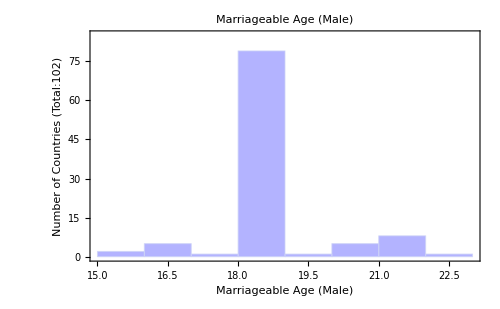

```mathematica
histoBoy=Histogram[boyMar,{1},PlotRange->{{15,23},{0,85}},PlotLabel->Style["Marriageable Age (Male)",Bold,Lighter[Blue]],Frame->True,ImageSize->500,ChartStyle->Lighter[Lighter[Lighter[Blue]]],FrameLabel->{"Marriageable Age (Male)","Number of Countries (Total:"<>ToString[Length[boyMar]]<>")"}]
```

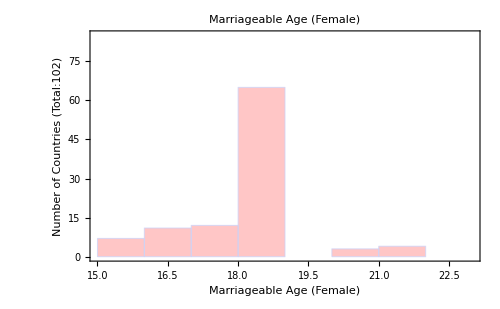

```mathematica
histoGirl=Histogram[girlMar,{1},PlotRange->{{15,23},{0,85}},Frame->True,PlotLabel->Style["Marriageable Age (Female)",Bold,Pink],ChartStyle->Lighter[Lighter[Pink]],FrameLabel->{"Marriageable Age (Female)","Number of Countries (Total:"<>ToString[Length[girlMar]]<>")"},ImageSize->500]
```

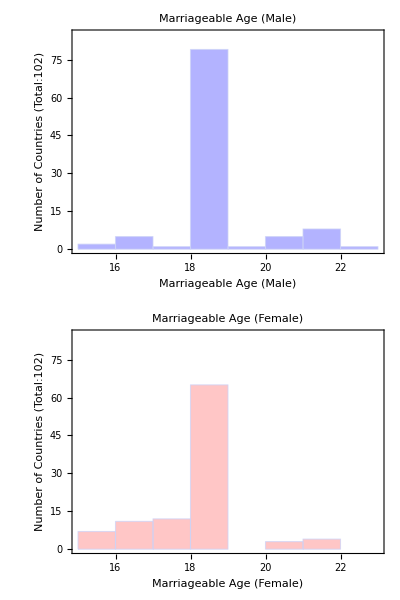

Export/histoBoyGirl.png

```mathematica
Grid[{{histoBoy},{histoGirl}}]
Export["Export/histoBoyGirl.png",%]
```

```mathematica
Sort[boyMar,#1>#2&]
```

{22.,21.,21.,21.,21.,21.,21.,21.,21.,20.,20.,20.,20.,20.,19.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,18.,17.,16.,16.,16.,16.,16.,15.,15.}

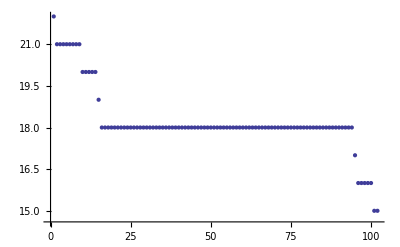

```mathematica
ListPlot[Sort[boyMar,#1>#2&]]
```

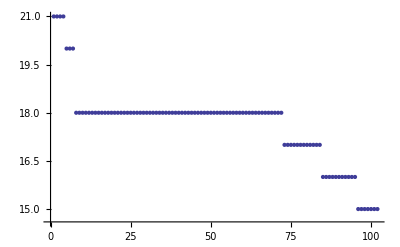

```mathematica
ListPlot[Sort[girlMar,#1>#2&]]
```

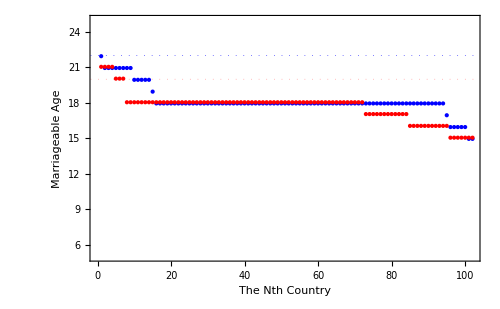

Export/ListPlotBoyGirl.png

```mathematica
ListPlot[{Sort[boyMar,#1>#2&]-0.05,Sort[girlMar,#1>#2&]+0.05},PlotStyle->{Blue,Red},PlotRange->{Automatic,{5,25}},ImageSize->500,Frame->True,FrameLabel->{"The Nth Country","Marriageable Age"},GridLines->{None,{{22,Directive[Dotted,Blue]},{20,Directive[Dotted,Pink]}}}]
Export["Export/ListPlotBoyGirl.png",%]
```

## What About Data Directly From Wikipedia Using Mathematica

Not Finished Yet

### Initial

```mathematica
urlMar="http://zh.wikipedia.org/wiki/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84#.E5.90.84.E5.9B.BD.E5.AE.B6.E5.92.8C.E5.9C.B0.E5.8C.BA.E6.B3.95.E5.AE.9A.E7.BB.93.E5.A9.9A.E5.B9.B4.E9.BE.84";
```

### Data Pre

Import the data

```mathematica
dataMar=Import[urlMar,"XMLObject"];
```

Import::chtype: First argument urlMar is not a valid file, directory, or URL specification.

Find out the proper elements.

XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/77/Flag_of_Algeria.svg/22px-Flag_of_Algeria.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/77/Flag_of_Algeria.svg/33px-Flag_of_Algeria.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/77/Flag_of_Algeria.svg/44px-Flag_of_Algeria.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%98%BF%E5%B0%94%E5%8F%8A%E5%88%A9%E4%BA%9A,title→\:963f\:5c14\:53ca\:5229\:4e9a},{\:963f\:5c14\:53ca\:5229\:4e9a}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{\:5982\:679c\:6839\:636e\:9700\:8981\:6216\:8005\:7279\:6b8a\:60c5\:51b5\:4e0b\:ff0c\:53ef\:4ee5\:9002\:5ea6\:964d\:4f4e\:5e74\:9f84\:8981\:6c42\:3002}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-9},{XMLElement[a,{shape→rect,href→#cite_note-9},{[9]}]}]}],
}]}]

```mathematica
dataSourceMar=Cases[dataMar,XMLElement[tr,{},{XMLElement[td,{colspan->1,rowspan->1},{XMLElement[span,{class->flagicon},{img_,}],XMLElement[a,{shape->rect,href->href1_,title->name_},{阿尔及利亚}]}],XMLElement[td,{colspan->1,rowspan->1},{
,XMLElement[div,{style->text-align:center;},{21}],}],XMLElement[td,{colspan->1,rowspan->1},{
,XMLElement[div,{style->text-align:center;},{18}],}],XMLElement[td,{colspan->1,rowspan->1},{
,XMLElement[div,{style->text-align:center;},{如果根据需要或者特殊情况下，可以适度降低年龄要求。}],}],XMLElement[td,{colspan->1,rowspan->1},{
,XMLElement[div,{style->text-align:center;},{XMLElement[sup,{class->reference,id->cite_ref-9},{XMLElement[a,{shape->rect,href->#cite_note-9},{[9]}]}]}],}]}]:>{name,First[labelb]}[[2]],Infinity]
```

```mathematica
data=Import[urlmar,"XMLObject"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{version→-//W3C//DTD HTML 4.01 Transitional//EN,class→client-nojs,dir→ltr,lang→zh,{http://www.w3.org/2000/xmlns/,xmlns}→http://www.w3.org/1999/xhtml},{XMLElement[head,{},{XMLElement[title,{},{法定结婚年龄 - 维基百科，自由的百科全书}],XMLElement[meta,{charset→UTF-8},{}],XMLElement[meta,{name→generator,content→MediaWiki 1.22wmf2},{}],XMLElement[link,{rel→alternate,type→application/x-wiki,title→编辑本页,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit},{}],XMLElement[link,{rel→edit,title→编辑本页,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit},{}],XMLElement[link,{rel→shortcut icon,href→//bits.wikimedia.org/favicon/wikipedia.ico},{}],XMLElement[link,{rel→search,type→application/opensearchdescription+xml,href→/w/opensearch_desc.php,title→Wikipedia (zh)},{}],XMLElement[link,{rel→EditURI,type→application/rsd+xml,href→//zh.wikipedia.org/w/api.php?action=rsd},{}],XMLElement[link,{hreflang→zh,rel→alternate,href→/zh/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{hreflang→zh-hans,rel→alternate,href→/zh-hans/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{hreflang→zh-hant,rel→alternate,href→/zh-hant/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{hreflang→zh-cn,rel→alternate,href→/zh-cn/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{hreflang→zh-hk,rel→alternate,href→/zh-hk/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{hreflang→zh-mo,rel→alternate,href→/zh-mo/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{hreflang→zh-sg,rel→alternate,href→/zh-sg/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{hreflang→zh-tw,rel→alternate,href→/zh-tw/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{}],XMLElement[link,{rel→copyright,href→//creativecommons.org/licenses/by-sa/3.0/},{}],XMLElement[link,{rel→alternate,type→application/atom+xml,title→Wikipedia的Atom,href→/w/index.php?title=Special:%E6%9C%80%E8%BF%91%E6%9B%B4%E6%94%B9&feed=atom},{}],XMLElement[link,{rel→stylesheet,href→//bits.wikimedia.org/zh.wikipedia.org/load.php?debug=false&lang=zh&modules=ext.gadget.AdvancedSiteNotices%2CReferenceTooltips%2CWikiMiniAtlas%2ChideConversionTab%2CinternalLinkHelper-altcolor%2Clarge-font%2CnoteTA%2CnoteTAvector%7Cext.wikihiero%7Cmediawiki.legacy.commonPrint%2Cshared%7Cmw.PopUpMediaTransform%7Cskins.vector&only=styles&skin=vector&*},{}],XMLElement[meta,{name→ResourceLoaderDynamicStyles,content→},{}],XMLElement[link,{rel→stylesheet,href→//bits.wikimedia.org/zh.wikipedia.org/load.php?debug=false&lang=zh&modules=site&only=styles&skin=vector&*},{}],XMLElement[style,{},{a:lang(ar),a:lang(ckb),a:lang(fa),a:lang(kk-arab),a:lang(mzn),a:lang(ps),a:lang(ur){text-decoration:none}
/* cache key: zhwiki:resourceloader:filter:minify-css:7:ea86fddf0b7328d662846f62cab00cde */}],XMLElement[script,{src→//bits.wikimedia.org/zh.wikipedia.org/load.php?debug=false&lang=zh&modules=startup&only=scripts&skin=vector&*},{}],XMLElement[script,{},{if(window.mw){
mw.config.set({"wgCanonicalNamespace":"","wgCanonicalSpecialPageName":false,"wgNamespaceNumber":0,"wgPageName":"法定结婚年龄","wgTitle":"法定结婚年龄","wgCurRevisionId":25671652,"wgArticleId":3025785,"wgIsArticle":true,"wgAction":"view","wgUserName":null,"wgUserGroups":["*"],"wgCategories":["含有俄語的條目","婚姻"],"wgBreakFrames":false,"wgPageContentLanguage":"zh","wgSeparatorTransformTable":["",""],"wgDigitTransformTable":["",""],"wgDefaultDateFormat":"zh","wgMonthNames":["","1月","2月","3月","4月","5月","6月","7月","8月","9月","10月","11月","12月"],"wgMonthNamesShort":["","1月","2月","3月","4月","5月","6月","7月","8月","9月","10月","11月","12月"],"wgRelevantPageName":"法定结婚年龄","wgUserVariant":"zh","wgRestrictionEdit":[],"wgRestrictionMove":[],"wgVectorEnabledModules":{"collapsiblenav":true,"collapsibletabs":true,"expandablesearch":false,"footercleanup":false,"sectioneditlinks":false,"experiments":true},"wgWikiEditorEnabledModules":{"toolbar":true,"dialogs":true,"hidesig":true,"templateEditor":false,"templates":false,"preview":false,"previewDialog":false,"publish":false,"toc":false},"wgVisualEditor":{"isPageWatched":false},"wikilove-recipient":"","wikilove-anon":0,"wgMFPhotoUploadEndpoint":"//commons.wikimedia.org/w/api.php","wgUseFormatCookie":{"name":"mf_mobileFormat","duration":-1,"path":"/","domain":"zh.wikipedia.org"},"wgStopMobileRedirectCookie":{"name":"stopMobileRedirect","duration":30,"domain":".wikipedia.org","path":"/"},"wgMFPhotoUploadAppendToDesc":"{{Uploaded from Mobile|platform=Web|version=}}\n{{subst:unc}}","wgImagesDisabled":false,"wgMFMode":"stable","wgIsPageEditable":true,"wgPreferredVariant":"zh","wgMFLoginHandshakeUrl":"//commons.wikimedia.org/wiki/Special:LoginHandshake?useformat=mobile","wgCategoryTreePageCategoryOptions":"{\"mode\":0,\"hideprefix\":20,\"showcount\":true,\"namespaces\":false}","Geo":{"city":"","country":""},"wgNoticeProject":"wikipedia"});
}}],XMLElement[script,{},{if(window.mw){
mw.loader.implement("user.options",function(){mw.user.options.set({"ccmeonemails":0,"cols":80,"date":"default","diffonly":0,"disablemail":0,"disablesuggest":0,"editfont":"default","editondblclick":0,"editsection":1,"editsectiononrightclick":0,"enotifminoredits":0,"enotifrevealaddr":0,"enotifusertalkpages":1,"enotifwatchlistpages":0,"extendwatchlist":0,"fancysig":0,"forceeditsummary":0,"gender":"unknown","hideminor":0,"hidepatrolled":0,"imagesize":2,"justify":0,"math":0,"minordefault":0,"newpageshidepatrolled":0,"nocache":0,"noconvertlink":0,"norollbackdiff":0,"numberheadings":0,"previewonfirst":0,"previewontop":1,"rcdays":7,"rclimit":50,"rememberpassword":0,"rows":25,"searchlimit":20,"showhiddencats":false,"showjumplinks":1,"shownumberswatching":1,"showtoc":1,"showtoolbar":1,"skin":"vector","stubthreshold":0,"thumbsize":4,"underline":2,"uselivepreview":0,"usenewrc":0,"watchcreations":1,"watchdefault":0,"watchdeletion":0,"watchlistdays":3,"watchlisthideanons":0,"watchlisthidebots":0,
"watchlisthideliu":0,"watchlisthideminor":0,"watchlisthideown":0,"watchlisthidepatrolled":0,"watchmoves":0,"wllimit":250,"useeditwarning":1,"vector-simplesearch":1,"vector-collapsiblenav":1,"usebetatoolbar":1,"usebetatoolbar-cgd":1,"wikilove-enabled":1,"variant":"zh","language":"zh","searchNs0":true,"searchNs1":false,"searchNs2":false,"searchNs3":false,"searchNs4":false,"searchNs5":false,"searchNs6":false,"searchNs7":false,"searchNs8":false,"searchNs9":false,"searchNs10":false,"searchNs11":false,"searchNs12":false,"searchNs13":false,"searchNs14":false,"searchNs15":false,"searchNs100":false,"searchNs101":false,"searchNs828":false,"searchNs829":false,"gadget-edit0":1,"gadget-WikiMiniAtlas":1,"gadget-ReferenceTooltips":1,"gadget-AdvancedSiteNotices":1,"gadget-hideConversionTab":1,"gadget-large-font":1,"gadget-internalLinkHelper-altcolor":1,"gadget-noteTA":1,"gadget-noteTAvector":1});},{},{});mw.loader.implement("user.tokens",function(){mw.user.tokens.set({"editToken":"+\\","patrolToken":
false,"watchToken":false});},{},{});
/* cache key: zhwiki:resourceloader:filter:minify-js:7:ed831820e43afeebcb4101c00c60e1b2 */
}}],XMLElement[script,{},{if(window.mw){
mw.loader.load(["mediawiki.page.startup","mediawiki.legacy.wikibits","mediawiki.legacy.ajax","ext.postEdit","wikibase.client.init","ext.centralNotice.bannerController"]);
}}],XMLElement[script,{src→//bits.wikimedia.org/geoiplookup},{}],XMLElement[link,{rel→dns-prefetch,href→//meta.wikimedia.org},{}]}],XMLElement[body,{class→mediawiki ltr sitedir-ltr ns-0 ns-subject page-法定结婚年龄 skin-vector action-view vector-animateLayout},{
		,XMLElement[div,{class→noprint,id→mw-page-base},{}],
		,XMLElement[div,{class→noprint,id→mw-head-base},{}],
		
		,XMLElement[div,{class→mw-body,id→content,role→main},{
			,XMLElement[a,{shape→rect,id→top},{}],
			,XMLElement[div,{id→mw-js-message,style→display:none;},{}],
						
			,XMLElement[div,{id→siteNotice},{XMLElement[script,{type→text/javascript},{
/* <![CDATA[ */
document.writeln("\x3cdiv id=\"localNotice\" lang=\"zh\" dir=\"ltr\"\x3e\x3c/div\x3e");
/* ]]> */
}]}],
			
						
			,XMLElement[h1,{class→firstHeading,id→firstHeading,lang→zh},{XMLElement[span,{dir→auto},{法定结婚年龄}]}],
			
			
			,XMLElement[div,{id→bodyContent},{
								
				,XMLElement[div,{id→siteSub},{维基百科，自由的百科全书}],
				
								
				,XMLElement[div,{id→contentSub},{}],
				
																
				,XMLElement[div,{class→mw-jump,id→jump-to-nav},{
					跳转至：					,XMLElement[a,{shape→rect,href→#mw-navigation},{导航}],、					,XMLElement[a,{shape→rect,href→#p-search},{搜索}],
				}],
				
								
				,XMLElement[div,{class→mw-content-ltr,dir→ltr,id→mw-content-text,lang→zh},{XMLElement[div,{class→metadata topicon noprint nopopups,id→noteTA-topicon,title→本页使用了标题或全文手工转换,style→display: none;},{XMLElement[img,{alt→本页使用了标题或全文手工转换,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/cd/Zh_conversion_icon_m.svg/35px-Zh_conversion_icon_m.svg.png,width→35,height→22,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/cd/Zh_conversion_icon_m.svg/53px-Zh_conversion_icon_m.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/cd/Zh_conversion_icon_m.svg/70px-Zh_conversion_icon_m.svg.png 2x},{}]}],
,XMLElement[div,{id→noteTA},{
,XMLElement[div,{id→noteTA-group},{
,XMLElement[div,{id→noteTA-group-.E5.9C.B0.E5.90.8D,data-noteta-group→地名},{}],
}],
}],
,XMLElement[p,{},{XMLElement[b,{},{法定最低结婚年龄}],，又称,XMLElement[b,{},{法定结婚年龄}],或,XMLElement[b,{},{适婚年龄}],，是指一个人被允许有权利（或经过父母同意或以其他形式）,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E7%BB%93%E5%A9%9A,title→结婚},{结婚}],的年龄。法定结婚年龄的标准因为国家或地区的不同而异，不过通常而言一般在18岁左右，但也有的国家或地区在有父母同意和/或法律许可或怀孕的情况下，允许人们在更年轻的年龄结婚。法定结婚年龄不能与,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E6%88%90%E5%B9%B4%E4%BA%BA%E5%B9%B4%E9%BE%84&action=edit&redlink=1,title→法定成年人年龄（页面不存在）},{法定成年人年龄}],、,XMLElement[a,{shape→rect,href→/wiki/%E6%9C%80%E4%BD%8E%E5%90%88%E6%B3%95%E6%80%A7%E4%BA%A4%E5%B9%B4%E9%BD%A1,title→最低合法性交年齡},{最低合法性交年齡}],、或某些地区的实际,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E5%88%9D%E6%AC%A1%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&redlink=1,title→初次结婚年龄（页面不存在）},{初次结婚年龄}],相互混淆，因为在,XMLElement[a,{shape→rect,href→/wiki/%E5%8F%91%E5%B1%95%E4%B8%AD%E5%9B%BD%E5%AE%B6,title→发展中国家},{发展中国家}],，,XMLElement[a,{shape→rect,href→/wiki/%E7%AB%A5%E5%A9%9A,title→童婚},{童婚}],非常普遍。}],
,XMLElement[p,{},{1962年，55个缔约国签署《,XMLElement[a,{shape→rect,class→extiw,href→//zh.wikisource.org/wiki/%E5%85%B3%E4%BA%8E%E5%A9%9A%E5%A7%BB%E7%9A%84%E5%90%8C%E6%84%8F%E3%80%81%E7%BB%93%E5%A9%9A%E6%9C%80%E4%BD%8E%E5%B9%B4%E9%BE%84%E5%8F%8A%E5%A9%9A%E5%A7%BB%E7%99%BB%E8%AE%B0%E7%9A%84%E5%85%AC%E7%BA%A6,title→s:关于婚姻的同意、结婚最低年龄及婚姻登记的公约},{关于婚姻的同意、结婚最低年龄及婚姻登记的公约}],》，该条约要求各方通过立法明确规定结婚最低年龄，从而凌驾于,XMLElement[a,{shape→rect,href→/wiki/%E4%B9%A0%E6%83%AF%E6%B3%95,title→习惯法},{习惯法}],、,XMLElement[a,{shape→rect,href→/wiki/%E5%AE%97%E6%97%8F,title→宗族},{宗族}],和,XMLElement[a,{shape→rect,href→/wiki/%E9%83%A8%E8%90%BD,title→部落},{部落}],的法律,XMLElement[sup,{class→reference,id→cite_ref-1},{XMLElement[a,{shape→rect,href→#cite_note-1},{[1]}]}], 。}],
,XMLElement[p,{},{当,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E5%AE%97%E6%95%99%E5%BE%8B%E6%B3%95&action=edit&redlink=1,title→宗教律法（页面不存在）},{宗教律法}],规定的法定结婚年龄低于国家法律之规定时，以国家规定为准，然而一些宗教律法并不承认国家法律的至高无上地位。}],
,XMLElement[table,{class→toc,id→toc},{XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{id→toctitle},{
,XMLElement[h2,{},{目录}],
}],
,XMLElement[ul,{},{XMLElement[li,{class→toclevel-1 tocsection-1},{XMLElement[a,{shape→rect,href→#.E5.8E.86.E5.8F.B2.E4.B8.8E.E8.A7.82.E7.82.B9},{XMLElement[span,{class→tocnumber},{1}], ,XMLElement[span,{class→toctext},{历史与观点}]}]}],XMLElement[li,{class→toclevel-1 tocsection-2},{XMLElement[a,{shape→rect,href→#.E5.90.84.E5.9B.BD.E5.AE.B6.E5.92.8C.E5.9C.B0.E5.8C.BA.E6.B3.95.E5.AE.9A.E7.BB.93.E5.A9.9A.E5.B9.B4.E9.BE.84},{XMLElement[span,{class→tocnumber},{2}], ,XMLElement[span,{class→toctext},{各国家和地区法定结婚年龄}]}],
,XMLElement[ul,{},{XMLElement[li,{class→toclevel-2 tocsection-3},{XMLElement[a,{shape→rect,href→#.E9.9D.9E.E6.B4.B2},{XMLElement[span,{class→tocnumber},{2.1}], ,XMLElement[span,{class→toctext},{非洲}]}]}],XMLElement[li,{class→toclevel-2 tocsection-4},{XMLElement[a,{shape→rect,href→#.E4.BA.9A.E6.B4.B2},{XMLElement[span,{class→tocnumber},{2.2}], ,XMLElement[span,{class→toctext},{亚洲}]}]}],XMLElement[li,{class→toclevel-2 tocsection-5},{XMLElement[a,{shape→rect,href→#.E6.AC.A7.E6.B4.B2},{XMLElement[span,{class→tocnumber},{2.3}], ,XMLElement[span,{class→toctext},{欧洲}]}]}],XMLElement[li,{class→toclevel-2 tocsection-6},{XMLElement[a,{shape→rect,href→#.E5.8C.97.E7.BE.8E.E6.B4.B2},{XMLElement[span,{class→tocnumber},{2.4}], ,XMLElement[span,{class→toctext},{北美洲}]}]}],XMLElement[li,{class→toclevel-2 tocsection-7},{XMLElement[a,{shape→rect,href→#.E5.8D.97.E7.BE.8E.E6.B4.B2},{XMLElement[span,{class→tocnumber},{2.5}], ,XMLElement[span,{class→toctext},{南美洲}]}]}],XMLElement[li,{class→toclevel-2 tocsection-8},{XMLElement[a,{shape→rect,href→#.E5.A4.A7.E6.B4.8B.E6.B4.B2},{XMLElement[span,{class→tocnumber},{2.6}], ,XMLElement[span,{class→toctext},{大洋洲}]}]}]}],
}],XMLElement[li,{class→toclevel-1 tocsection-9},{XMLElement[a,{shape→rect,href→#.E5.8F.82.E8.80.83},{XMLElement[span,{class→tocnumber},{3}], ,XMLElement[span,{class→toctext},{参考}]}]}]}],
}]}]}],
,XMLElement[h2,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=1,title→编辑章节：历史与观点},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E5.8E.86.E5.8F.B2.E4.B8.8E.E8.A7.82.E7.82.B9},{历史与观点}]}],
,XMLElement[p,{},{在历史上，世界各地通常认为，一个人是否可以,XMLElement[a,{shape→rect,href→/wiki/%E4%BA%BA%E7%B1%BB%E6%80%A7%E8%A1%8C%E4%B8%BA,title→人类性行为},{性结合}],，取决于家族的决定或部落的习俗。大多数情况下，这通常决定于人类,XMLElement[a,{shape→rect,href→/wiki/%E9%9D%92%E6%98%A5%E6%9C%9F,title→青春期},{青春期}],的一些特征，如女子来,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E6%9C%88%E7%BB%8F,title→月经},{月经}],或男子开始长,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E9%98%B4%E6%AF%9B,title→阴毛},{阴毛}],XMLElement[sup,{class→reference,id→cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-0},{XMLElement[a,{shape→rect,href→#cite_note-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent-2},{[2]}]}],。}],
,XMLElement[p,{},{在,XMLElement[a,{shape→rect,href→/wiki/%E5%8F%A4%E7%BD%97%E9%A9%AC,title→古罗马},{古罗马}],，女子在青春期到来后很快就结婚生子的现象非常普遍。}],
,XMLElement[p,{},{在古,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E6%97%A5%E5%B0%94%E6%9B%BC,title→日尔曼},{日尔曼部落}],中，,XMLElement[a,{shape→rect,href→/wiki/%E6%96%B0%E5%A8%98,title→新娘},{新娘}],和,XMLElement[a,{shape→rect,href→/wiki/%E6%96%B0%E9%83%8E,title→新郎},{新郎}],年龄大致相同，而大于古罗马时期，如,XMLElement[a,{shape→rect,href→/wiki/%E5%A1%94%E8%A5%BF%E4%BD%97,title→塔西佗},{塔西佗}],就曾经说过,XMLElement[sup,{class→reference,id→cite_ref-3},{XMLElement[a,{shape→rect,href→#cite_note-3},{[3]}]}],：}],
,XMLElement[blockquote,{},{
,XMLElement[p,{},{他们是迟婚的，所以有着充沛无比的精力。女孩子也并不很早就结婚，男女都要到达同样的年龄和身材发育到同样的程度以后才结为配偶，因而子女长大后也有着与父母同样充沛的精力。}],
}],
,XMLElement[p,{},{XMLElement[a,{shape→rect,href→/wiki/%E4%BA%9A%E9%87%8C%E5%A3%AB%E5%A4%9A%E5%BE%B7,title→亚里士多德},{亚里士多德}],认为，男子37岁，女子18岁是结婚的最佳年龄，而在,XMLElement[a,{shape→rect,href→/wiki/7%E4%B8%96%E7%BA%AA,title→7世纪},{7世纪}],的《,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E8%A5%BF%E5%93%A5%E7%89%B9%E6%B3%95%E5%85%B8&action=edit&redlink=1,title→西哥特法典（页面不存在）},{西哥特法典}],》中，认为男子和女子在20岁时处于黄金时期，因此可以推测大多数当时的日尔曼妇女跟她们的丈夫一样，至少在20岁时结婚,XMLElement[sup,{class→reference,id→cite_ref-4},{XMLElement[a,{shape→rect,href→#cite_note-4},{[4]}]}],。}],
,XMLElement[p,{},{允许结婚年龄的最早记录可以回溯到800年前的,XMLElement[a,{shape→rect,href→/wiki/%E8%8B%B1%E6%A0%BC%E5%85%B0,title→英格兰},{英格兰}],：1275年，英格兰发布《,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E5%A8%81%E6%96%AF%E6%95%8F%E6%96%AF%E7%89%B9%E7%AC%AC%E4%B8%80%E6%B3%95%E6%A1%88&action=edit&redlink=1,title→威斯敏斯特第一法案（页面不存在）},{威斯敏斯特第一法案}],》，其中关于,XMLElement[a,{shape→rect,href→/wiki/%E5%BC%BA%E5%A5%B8,title→强奸},{强奸}],规定中，其是否构成强奸，不是出于少女自愿与否，而是出于该女子的年龄是否不超过一定的年龄,XMLElement[sup,{class→reference,id→cite_ref-5},{XMLElement[a,{shape→rect,href→#cite_note-5},{[5]}]}],。法学家爱德华·科可（17世纪英格兰人）认为，过了“一定的年龄”即表示女子可以结婚，在当时，这个年龄为12岁。,XMLElement[sup,{class→reference,id→cite_ref-Stephen_Robertson.2C_University_of_Sydney.2C_Australia_6-0},{XMLElement[a,{shape→rect,href→#cite_note-Stephen_Robertson.2C_University_of_Sydney.2C_Australia-6},{[6]}]}]}],
,XMLElement[p,{},{在,XMLElement[a,{shape→rect,href→/wiki/%E4%B8%AD%E4%B8%96%E7%BA%AA,title→中世纪},{中世纪}],的,XMLElement[a,{shape→rect,href→/wiki/%E6%AC%A7%E6%B4%B2,title→欧洲},{欧洲}],，,XMLElement[a,{shape→rect,href→/wiki/12%E4%B8%96%E7%BA%AA,title→12世纪},{12世纪}],XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E6%A0%BC%E6%8B%89%E6%8F%90%E5%AE%89_(%E6%B3%95%E5%AE%98)&action=edit&redlink=1,title→格拉提安 (法官)（页面不存在）},{格拉提安}],提出了《,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E6%A0%BC%E6%8B%89%E5%A5%87%E6%95%99%E4%BB%A4&action=edit&redlink=1,title→格拉奇教令（页面不存在）},{格拉奇教令}],》，允许人们在12岁至14岁时结婚，但同时也认为如果当事人大于7岁，那么这一婚姻亦是可以允许的。除非在未到青春期前双方取消婚约，或者他们已经结婚，那么就是这一婚姻就是有效的。值得注意的是，格拉提安因为允许小于7岁的儿童结婚而受到尊敬，尽管他曾经说过：“有记录显示，有人在2至3岁时就结婚。”,XMLElement[sup,{class→reference,id→cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-1},{XMLElement[a,{shape→rect,href→#cite_note-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent-2},{[2]}]}]}],
,XMLElement[p,{},{尽管如此，在,XMLElement[a,{shape→rect,href→/wiki/%E8%A5%BF%E5%8C%97%E6%AC%A7,title→西北欧},{西北欧}],的大多数地区，在非常小的时候就结婚仍然是非常罕见的。在1619年至1660年,XMLElement[a,{shape→rect,href→/wiki/%E5%9D%8E%E7%89%B9%E4%BC%AF%E9%9B%B7%E5%A4%A7%E4%B8%BB%E6%95%99,title→坎特伯雷大主教},{坎特伯雷大主教}],管辖范围内的1000例结婚事件中，仅有一个新娘13岁，4个15岁，12个16岁，17个17岁，而其他的966个新娘在结婚时至少19岁。教会规定，在没有父母同意的情况下，新娘和新郎必须至少21岁方可以结婚。在那1000例结婚事件中，新娘通常在22岁左右，而新郎通常在24岁左右，平均结婚年龄则为新郎27.75岁，新娘24岁。,XMLElement[sup,{class→reference,id→cite_ref-Laslett.2C_Peter_1965._p_82_7-0},{XMLElement[a,{shape→rect,href→#cite_note-Laslett.2C_Peter_1965._p_82-7},{[7]}]}],尽管在当时有欧洲,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E8%B4%B5%E6%97%8F,title→贵族},{贵族}],女子结婚非常早，但那毕竟属于少数群体,XMLElement[sup,{class→reference,id→cite_ref-8},{XMLElement[a,{shape→rect,href→#cite_note-8},{[8]}]}],。据坎特伯雷的婚姻记录显示，哪怕是贵族，在非常早的年龄结婚同样是非常罕见的。,XMLElement[sup,{class→reference,id→cite_ref-Laslett.2C_Peter_1965._p_82_7-1},{XMLElement[a,{shape→rect,href→#cite_note-Laslett.2C_Peter_1965._p_82-7},{[7]}]}]}],
,XMLElement[p,{},{当时还属于,XMLElement[a,{shape→rect,href→/wiki/%E6%AE%96%E6%B0%91%E5%9C%B0,title→殖民地},{殖民地}],的美国，延续了英国的传统和法律规定，如，玛丽·哈撒韦（,XMLElement[a,{shape→rect,href→/wiki/%E5%BC%97%E5%90%89%E5%B0%BC%E4%BA%9A%E5%B7%9E,title→弗吉尼亚州},{弗吉尼亚州}],，1689年）在9岁时嫁给了威廉·威廉姆斯。爱德华·科可明确地说：“女子在12岁时就结婚是非常正常的一件事，在这个年龄，如果一个女孩在9岁时成为男人的妻子，那么她就有权利继承丈夫的财产——哪怕她的丈夫只有四岁。,XMLElement[sup,{class→reference,id→cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-2},{XMLElement[a,{shape→rect,href→#cite_note-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent-2},{[2]}]}]}],
,XMLElement[p,{},{关于人们实际结婚年龄的数据很难找到，如在英格兰，,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E8%BF%91%E4%BB%A3,title→近代},{近代}],唯一可靠的结婚年龄数据来源于本人死亡后的记录。困扰并不仅限于数据的匮乏，还限于那些当事人的年龄——越完整的记录，方能越可能揭示早婚的确切年龄。此外，在,XMLElement[a,{shape→rect,href→/wiki/20%E4%B8%96%E7%BA%AA,title→20世纪},{20世纪}],和,XMLElement[a,{shape→rect,href→/wiki/21%E4%B8%96%E7%BA%AA,title→21世纪},{21世纪}],，,XMLElement[a,{shape→rect,href→/wiki/%E5%8E%86%E5%8F%B2%E5%AD%A6%E5%AE%B6,title→历史学家},{历史学家}],有时不愿意接受相关早婚的数据，认为这些数据属于伪造的数据。,XMLElement[sup,{class→reference,id→cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-3},{XMLElement[a,{shape→rect,href→#cite_note-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent-2},{[2]}]}]}],
,XMLElement[h2,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=2,title→编辑章节：各国家和地区法定结婚年龄},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E5.90.84.E5.9B.BD.E5.AE.B6.E5.92.8C.E5.9C.B0.E5.8C.BA.E6.B3.95.E5.AE.9A.E7.BB.93.E5.A9.9A.E5.B9.B4.E9.BE.84},{各国家和地区法定结婚年龄}]}],
,XMLElement[h3,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=3,title→编辑章节：非洲},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E9.9D.9E.E6.B4.B2},{非洲}]}],
,XMLElement[table,{class→wikitable sortable},{XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→2,width→150},{国家}],XMLElement[th,{colspan→2,rowspan→1,width→200},{法定结婚年龄}],XMLElement[th,{colspan→1,rowspan→2,width→550},{备注}],XMLElement[th,{colspan→1,rowspan→2,width→100},{参考}]}],XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{男性}],
}],XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{女性}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/77/Flag_of_Algeria.svg/22px-Flag_of_Algeria.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/77/Flag_of_Algeria.svg/33px-Flag_of_Algeria.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/77/Flag_of_Algeria.svg/44px-Flag_of_Algeria.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%98%BF%E5%B0%94%E5%8F%8A%E5%88%A9%E4%BA%9A,title→阿尔及利亚},{阿尔及利亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{如果根据需要或者特殊情况下，可以适度降低年龄要求。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-9},{XMLElement[a,{shape→rect,href→#cite_note-9},{[9]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/fe/Flag_of_Egypt.svg/22px-Flag_of_Egypt.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/fe/Flag_of_Egypt.svg/33px-Flag_of_Egypt.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/fe/Flag_of_Egypt.svg/44px-Flag_of_Egypt.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%9F%83%E5%8F%8A,title→埃及},{埃及}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{2008年，女性年龄由16岁提升至18岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-10},{XMLElement[a,{shape→rect,href→#cite_note-10},{[10]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/71/Flag_of_Ethiopia.svg/22px-Flag_of_Ethiopia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/71/Flag_of_Ethiopia.svg/33px-Flag_of_Ethiopia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/71/Flag_of_Ethiopia.svg/44px-Flag_of_Ethiopia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%9F%83%E5%A1%9E%E4%BF%84%E6%AF%94%E4%BA%9A,title→埃塞俄比亚},{埃塞俄比亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-books.google.com_11-0},{XMLElement[a,{shape→rect,href→#cite_note-books.google.com-11},{[11]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/49/Flag_of_Kenya.svg/22px-Flag_of_Kenya.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/49/Flag_of_Kenya.svg/33px-Flag_of_Kenya.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/49/Flag_of_Kenya.svg/44px-Flag_of_Kenya.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%82%AF%E5%B0%BC%E4%BA%9A,title→肯尼亚},{肯尼亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-12},{XMLElement[a,{shape→rect,href→#cite_note-12},{[12]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/05/Flag_of_Libya.svg/22px-Flag_of_Libya.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/05/Flag_of_Libya.svg/33px-Flag_of_Libya.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/05/Flag_of_Libya.svg/44px-Flag_of_Libya.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%88%A9%E6%AF%94%E4%BA%9A,title→利比亚},{利比亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-13},{XMLElement[a,{shape→rect,href→#cite_note-13},{[13]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/b/bc/Flag_of_Madagascar.svg/22px-Flag_of_Madagascar.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/b/bc/Flag_of_Madagascar.svg/33px-Flag_of_Madagascar.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/b/bc/Flag_of_Madagascar.svg/44px-Flag_of_Madagascar.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%A9%AC%E8%BE%BE%E5%8A%A0%E6%96%AF%E5%8A%A0,title→马达加斯加},{马达加斯加}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-14},{XMLElement[a,{shape→rect,href→#cite_note-14},{[14]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/92/Flag_of_Mali.svg/22px-Flag_of_Mali.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/92/Flag_of_Mali.svg/33px-Flag_of_Mali.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/92/Flag_of_Mali.svg/44px-Flag_of_Mali.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%A9%AC%E9%87%8C%E5%85%B1%E5%92%8C%E5%9B%BD,title→马里共和国},{马里}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18或15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18或15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-15},{XMLElement[a,{shape→rect,href→#cite_note-15},{[15]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/2c/Flag_of_Morocco.svg/22px-Flag_of_Morocco.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/2c/Flag_of_Morocco.svg/33px-Flag_of_Morocco.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/2c/Flag_of_Morocco.svg/44px-Flag_of_Morocco.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%91%A9%E6%B4%9B%E5%93%A5,title→摩洛哥},{摩洛哥}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在农村地区，许多女子在18岁以下结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-16},{XMLElement[a,{shape→rect,href→#cite_note-16},{[16]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/f4/Flag_of_Niger.svg/22px-Flag_of_Niger.svg.png,width→22,height→19,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/f4/Flag_of_Niger.svg/33px-Flag_of_Niger.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/f4/Flag_of_Niger.svg/44px-Flag_of_Niger.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%B0%BC%E6%97%A5%E5%B0%94,title→尼日尔},{尼日尔}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-17},{XMLElement[a,{shape→rect,href→#cite_note-17},{[17]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/79/Flag_of_Nigeria.svg/22px-Flag_of_Nigeria.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/79/Flag_of_Nigeria.svg/33px-Flag_of_Nigeria.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/79/Flag_of_Nigeria.svg/44px-Flag_of_Nigeria.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%A5%88%E5%8F%8A%E5%88%A9%E4%BA%9E,title→奈及利亞},{奈及利亞}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-books.google.com_11-1},{XMLElement[a,{shape→rect,href→#cite_note-books.google.com-11},{[11]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/fd/Flag_of_Senegal.svg/22px-Flag_of_Senegal.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/fd/Flag_of_Senegal.svg/33px-Flag_of_Senegal.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/fd/Flag_of_Senegal.svg/44px-Flag_of_Senegal.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%A1%9E%E5%86%85%E5%8A%A0%E5%B0%94,title→塞内加尔},{塞内加尔}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-18},{XMLElement[a,{shape→rect,href→#cite_note-18},{[18]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/a/a0/Flag_of_Somalia.svg/22px-Flag_of_Somalia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/a/a0/Flag_of_Somalia.svg/33px-Flag_of_Somalia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/a/a0/Flag_of_Somalia.svg/44px-Flag_of_Somalia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E7%B4%A2%E9%A6%AC%E9%87%8C,title→索馬里},{索馬里}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{需经监护人同意。法院在特殊情况下，可以判定豁免最低结婚年龄}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-19},{XMLElement[a,{shape→rect,href→#cite_note-19},{[19]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/a/af/Flag_of_South_Africa.svg/22px-Flag_of_South_Africa.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/a/af/Flag_of_South_Africa.svg/33px-Flag_of_South_Africa.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/a/af/Flag_of_South_Africa.svg/44px-Flag_of_South_Africa.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8D%97%E9%9D%9E,title→南非},{南非}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{2006年允许,XMLElement[a,{shape→rect,href→/wiki/%E5%90%8C%E6%80%A7%E5%A9%9A%E5%A7%BB,title→同性婚姻},{同性结婚}]}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-20},{XMLElement[a,{shape→rect,href→#cite_note-20},{[20]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/01/Flag_of_Sudan.svg/22px-Flag_of_Sudan.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/01/Flag_of_Sudan.svg/33px-Flag_of_Sudan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/01/Flag_of_Sudan.svg/44px-Flag_of_Sudan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E8%8B%8F%E4%B8%B9,title→苏丹},{苏丹}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{青春期}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{青春期}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{需双方当事人同意。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-21},{XMLElement[a,{shape→rect,href→#cite_note-21},{[21]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/7a/Flag_of_South_Sudan.svg/22px-Flag_of_South_Sudan.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/7a/Flag_of_South_Sudan.svg/33px-Flag_of_South_Sudan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/7a/Flag_of_South_Sudan.svg/44px-Flag_of_South_Sudan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8D%97%E8%98%87%E4%B8%B9,title→南蘇丹},{南蘇丹}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{需双方当事人同意。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-22},{XMLElement[a,{shape→rect,href→#cite_note-22},{[22]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/3/38/Flag_of_Tanzania.svg/22px-Flag_of_Tanzania.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/3/38/Flag_of_Tanzania.svg/33px-Flag_of_Tanzania.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/3/38/Flag_of_Tanzania.svg/44px-Flag_of_Tanzania.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%9D%A6%E6%A1%91%E5%B0%BC%E4%BA%9A,title→坦桑尼亚},{坦桑尼亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特定情况下，法院可以允许在14岁时结婚。当地刑法典规定，按照当地风俗且不是出于宗教目的，女子可以在12岁以下结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-23},{XMLElement[a,{shape→rect,href→#cite_note-23},{[23]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/ce/Flag_of_Tunisia.svg/22px-Flag_of_Tunisia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/ce/Flag_of_Tunisia.svg/33px-Flag_of_Tunisia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/ce/Flag_of_Tunisia.svg/44px-Flag_of_Tunisia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%AA%81%E5%B0%BC%E8%A5%BF%E4%BA%9E,title→突尼西亞},{突尼西亞}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{如果根据需要或者特殊情况下，可以适度降低年龄要求。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-24},{XMLElement[a,{shape→rect,href→#cite_note-24},{[24]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/6/6a/Flag_of_Zimbabwe.svg/22px-Flag_of_Zimbabwe.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/6/6a/Flag_of_Zimbabwe.svg/33px-Flag_of_Zimbabwe.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/6/6a/Flag_of_Zimbabwe.svg/44px-Flag_of_Zimbabwe.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E6%B4%A5%E5%B7%B4%E5%B8%83%E9%9F%A6,title→津巴布韦},{津巴布韦}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-25},{XMLElement[a,{shape→rect,href→#cite_note-25},{[25]}]}]}],
}]}]}],
,XMLElement[h3,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=4,title→编辑章节：亚洲},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E4.BA.9A.E6.B4.B2},{亚洲}]}],
,XMLElement[table,{class→wikitable sortable},{XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→2,width→150},{国家}],XMLElement[th,{colspan→2,rowspan→1,width→200},{法定结婚年龄}],XMLElement[th,{colspan→1,rowspan→2,width→550},{备注}],XMLElement[th,{colspan→1,rowspan→2,width→100},{参考}]}],XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{男性}],
}],XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{女性}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Afghanistan.svg/22px-Flag_of_Afghanistan.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Afghanistan.svg/33px-Flag_of_Afghanistan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Afghanistan.svg/44px-Flag_of_Afghanistan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%98%BF%E5%AF%8C%E6%B1%97,title→阿富汗},{阿富汗}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{大多数女子在16岁以下结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-26},{XMLElement[a,{shape→rect,href→#cite_note-26},{[26]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/2f/Flag_of_Armenia.svg/22px-Flag_of_Armenia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/2f/Flag_of_Armenia.svg/33px-Flag_of_Armenia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/2f/Flag_of_Armenia.svg/44px-Flag_of_Armenia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BA%9E%E7%BE%8E%E5%B0%BC%E4%BA%9E,title→亞美尼亞},{亚美尼亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-27},{XMLElement[a,{shape→rect,href→#cite_note-27},{[27]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/d/dd/Flag_of_Azerbaijan.svg/22px-Flag_of_Azerbaijan.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/d/dd/Flag_of_Azerbaijan.svg/33px-Flag_of_Azerbaijan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/d/dd/Flag_of_Azerbaijan.svg/44px-Flag_of_Azerbaijan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%98%BF%E5%A1%9E%E6%8B%9C%E7%96%86,title→阿塞拜疆},{阿塞拜疆}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特殊情况下，男女可以在17岁和16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-demaz.org_28-0},{XMLElement[a,{shape→rect,href→#cite_note-demaz.org-28},{[28]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/f9/Flag_of_Bangladesh.svg/22px-Flag_of_Bangladesh.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/f9/Flag_of_Bangladesh.svg/33px-Flag_of_Bangladesh.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/f9/Flag_of_Bangladesh.svg/44px-Flag_of_Bangladesh.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%AD%9F%E5%8A%A0%E6%8B%89,title→孟加拉},{孟加拉国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{虽然有时法院会许可在低于法定结婚年龄的情况下结婚，但此通常会被认为无效。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-29},{XMLElement[a,{shape→rect,href→#cite_note-29},{[29]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9c/Flag_of_Brunei.svg/22px-Flag_of_Brunei.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9c/Flag_of_Brunei.svg/33px-Flag_of_Brunei.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9c/Flag_of_Brunei.svg/44px-Flag_of_Brunei.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%96%87%E8%8E%B1,title→文莱},{文莱}]}],XMLElement[td,{colspan→2,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{没有规定最低结婚年龄}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-30},{XMLElement[a,{shape→rect,href→#cite_note-30},{[30]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/fa/Flag_of_the_People%27s_Republic_of_China.svg/22px-Flag_of_the_People%27s_Republic_of_China.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/fa/Flag_of_the_People%27s_Republic_of_China.svg/33px-Flag_of_the_People%27s_Republic_of_China.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/fa/Flag_of_the_People%27s_Republic_of_China.svg/44px-Flag_of_the_People%27s_Republic_of_China.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%B8%AD%E5%8D%8E%E4%BA%BA%E6%B0%91%E5%85%B1%E5%92%8C%E5%9B%BD,title→中华人民共和国},{中华人民共和国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{22}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-China2006_31-0},{XMLElement[a,{shape→rect,href→#cite_note-China2006-31},{[31]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Georgia.svg/22px-Flag_of_Georgia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Georgia.svg/33px-Flag_of_Georgia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Georgia.svg/44px-Flag_of_Georgia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%A0%BC%E9%B2%81%E5%90%89%E4%BA%9A,title→格鲁吉亚},{格鲁吉亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-32},{XMLElement[a,{shape→rect,href→#cite_note-32},{[32]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/5/5b/Flag_of_Hong_Kong.svg/22px-Flag_of_Hong_Kong.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/5/5b/Flag_of_Hong_Kong.svg/33px-Flag_of_Hong_Kong.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/5/5b/Flag_of_Hong_Kong.svg/44px-Flag_of_Hong_Kong.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%A6%99%E6%B8%AF,title→香港},{香港}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-33},{XMLElement[a,{shape→rect,href→#cite_note-33},{[33]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/41/Flag_of_India.svg/22px-Flag_of_India.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/41/Flag_of_India.svg/33px-Flag_of_India.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/41/Flag_of_India.svg/44px-Flag_of_India.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8D%B0%E5%BA%A6,title→印度},{印度}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{如果双方中有一方结婚时年龄小于此年龄，则可以宣布该婚姻无效。按法律规定，16岁以下的婚姻是无效的，而16岁至17岁的婚姻则是可撤销的。2012年，,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=%E5%8D%B0%E5%BA%A6%E6%9C%80%E9%AB%98%E6%B3%95%E9%99%A2&action=edit&redlink=1,title→印度最高法院（页面不存在）},{印度最高法院}],宣布，,XMLElement[a,{shape→rect,href→/wiki/%E7%A9%86%E6%96%AF%E6%9E%97,title→穆斯林},{穆斯林}],妇女可以在15岁时结婚。但有调查显示，在印度，童婚现象非常普遍，而且未被法院宣布无效。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-34},{XMLElement[a,{shape→rect,href→#cite_note-34},{[34]}]}],XMLElement[sup,{class→reference,id→cite_ref-lawcommissionofindia.nic.in_35-0},{XMLElement[a,{shape→rect,href→#cite_note-lawcommissionofindia.nic.in-35},{[35]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9f/Flag_of_Indonesia.svg/22px-Flag_of_Indonesia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9f/Flag_of_Indonesia.svg/33px-Flag_of_Indonesia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9f/Flag_of_Indonesia.svg/44px-Flag_of_Indonesia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8D%B0%E5%BA%A6%E5%B0%BC%E8%A5%BF%E4%BA%9A,title→印度尼西亚},{印尼}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{19}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母同意，可以在再小的年龄结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-36},{XMLElement[a,{shape→rect,href→#cite_note-36},{[36]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/ca/Flag_of_Iran.svg/22px-Flag_of_Iran.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/ca/Flag_of_Iran.svg/33px-Flag_of_Iran.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/ca/Flag_of_Iran.svg/44px-Flag_of_Iran.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BC%8A%E6%9C%97,title→伊朗},{伊朗}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-37},{XMLElement[a,{shape→rect,href→#cite_note-37},{[37]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/f6/Flag_of_Iraq.svg/22px-Flag_of_Iraq.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/f6/Flag_of_Iraq.svg/33px-Flag_of_Iraq.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/f6/Flag_of_Iraq.svg/44px-Flag_of_Iraq.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BC%8A%E6%8B%89%E5%85%8B,title→伊拉克},{伊拉克}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{如果身体健康、体质允许，且经监护人同意的情况下，可以在15岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-38},{XMLElement[a,{shape→rect,href→#cite_note-38},{[38]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/d/d4/Flag_of_Israel.svg/22px-Flag_of_Israel.svg.png,width→22,height→16,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/d/d4/Flag_of_Israel.svg/33px-Flag_of_Israel.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/d/d4/Flag_of_Israel.svg/44px-Flag_of_Israel.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BB%A5%E8%89%B2%E5%88%97,title→以色列},{以色列}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-39},{XMLElement[a,{shape→rect,href→#cite_note-39},{[39]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9e/Flag_of_Japan.svg/22px-Flag_of_Japan.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9e/Flag_of_Japan.svg/33px-Flag_of_Japan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9e/Flag_of_Japan.svg/44px-Flag_of_Japan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%97%A5%E6%9C%AC,title→日本},{日本}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母的同意下，男女可以分别是在18岁和16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-40},{XMLElement[a,{shape→rect,href→#cite_note-40},{[40]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/c0/Flag_of_Jordan.svg/22px-Flag_of_Jordan.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/c0/Flag_of_Jordan.svg/33px-Flag_of_Jordan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/c0/Flag_of_Jordan.svg/44px-Flag_of_Jordan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%BA%A6%E6%97%A6,title→约旦},{约旦}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{女子低于18岁结婚时，需要丈夫年龄不低于20岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-41},{XMLElement[a,{shape→rect,href→#cite_note-41},{[41]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/d/d3/Flag_of_Kazakhstan.svg/22px-Flag_of_Kazakhstan.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/d/d3/Flag_of_Kazakhstan.svg/33px-Flag_of_Kazakhstan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/d/d3/Flag_of_Kazakhstan.svg/44px-Flag_of_Kazakhstan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E5%93%88%E8%96%A9%E5%85%8B,title→哈薩克},{哈萨克斯坦}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特殊情况下，经由父母同意，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-42},{XMLElement[a,{shape→rect,href→#cite_note-42},{[42]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/09/Flag_of_South_Korea.svg/22px-Flag_of_South_Korea.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/09/Flag_of_South_Korea.svg/33px-Flag_of_South_Korea.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/09/Flag_of_South_Korea.svg/44px-Flag_of_South_Korea.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E9%9F%93%E5%9C%8B,title→韓國},{韩国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{如果父母同意，可以在未成年时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-43},{XMLElement[a,{shape→rect,href→#cite_note-43},{[43]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/a/aa/Flag_of_Kuwait.svg/22px-Flag_of_Kuwait.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/a/aa/Flag_of_Kuwait.svg/33px-Flag_of_Kuwait.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/a/aa/Flag_of_Kuwait.svg/44px-Flag_of_Kuwait.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%A7%91%E5%A8%81%E7%89%B9,title→科威特},{科威特}]}],XMLElement[td,{colspan→2,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{没有规定最低结婚年龄}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-44},{XMLElement[a,{shape→rect,href→#cite_note-44},{[44]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/c7/Flag_of_Kyrgyzstan.svg/22px-Flag_of_Kyrgyzstan.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/c7/Flag_of_Kyrgyzstan.svg/33px-Flag_of_Kyrgyzstan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/c7/Flag_of_Kyrgyzstan.svg/44px-Flag_of_Kyrgyzstan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E5%90%89%E7%88%BE%E5%90%89%E6%96%AF,title→吉爾吉斯},{吉尔吉斯斯坦}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-45},{XMLElement[a,{shape→rect,href→#cite_note-45},{[45]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/5/59/Flag_of_Lebanon.svg/22px-Flag_of_Lebanon.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/5/59/Flag_of_Lebanon.svg/33px-Flag_of_Lebanon.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/5/59/Flag_of_Lebanon.svg/44px-Flag_of_Lebanon.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%BB%8E%E5%B7%B4%E5%AB%A9,title→黎巴嫩},{黎巴嫩}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-46},{XMLElement[a,{shape→rect,href→#cite_note-46},{[46]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/6/66/Flag_of_Malaysia.svg/22px-Flag_of_Malaysia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/6/66/Flag_of_Malaysia.svg/33px-Flag_of_Malaysia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/6/66/Flag_of_Malaysia.svg/44px-Flag_of_Malaysia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%A9%AC%E6%9D%A5%E8%A5%BF%E4%BA%9A,title→马来西亚},{马来西亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母同意可以在18岁时结婚，当地伊斯兰教允许16岁以下的穆斯林少女结婚，其中一些14岁的少女结婚也是被许可的。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-47},{XMLElement[a,{shape→rect,href→#cite_note-47},{[47]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Maldives.svg/22px-Flag_of_Maldives.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Maldives.svg/33px-Flag_of_Maldives.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Maldives.svg/44px-Flag_of_Maldives.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%A9%AC%E5%B0%94%E4%BB%A3%E5%A4%AB,title→马尔代夫},{马尔代夫}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15岁是由当地习俗所决定，但当地政府提倡16岁以后结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-48},{XMLElement[a,{shape→rect,href→#cite_note-48},{[48]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9b/Flag_of_Nepal.svg/16px-Flag_of_Nepal.svg.png,width→16,height→20,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9b/Flag_of_Nepal.svg/25px-Flag_of_Nepal.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9b/Flag_of_Nepal.svg/33px-Flag_of_Nepal.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%B0%BC%E6%B3%8A%E5%B0%94,title→尼泊尔},{尼泊尔}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母许可，男女可以在18/16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-49},{XMLElement[a,{shape→rect,href→#cite_note-49},{[49]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/3/32/Flag_of_Pakistan.svg/22px-Flag_of_Pakistan.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/3/32/Flag_of_Pakistan.svg/33px-Flag_of_Pakistan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/3/32/Flag_of_Pakistan.svg/44px-Flag_of_Pakistan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%B7%B4%E5%9F%BA%E6%96%AF%E5%9D%A6,title→巴基斯坦},{巴基斯坦}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-50},{XMLElement[a,{shape→rect,href→#cite_note-50},{[50]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/00/Flag_of_Palestine.svg/22px-Flag_of_Palestine.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/00/Flag_of_Palestine.svg/33px-Flag_of_Palestine.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/00/Flag_of_Palestine.svg/44px-Flag_of_Palestine.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%B7%B4%E5%8B%92%E6%96%AF%E5%9D%A6%E5%9B%BD,title→巴勒斯坦国},{巴勒斯坦国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-51},{XMLElement[a,{shape→rect,href→#cite_note-51},{[51]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/4c/Flag_of_Mongolia.svg/22px-Flag_of_Mongolia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/4c/Flag_of_Mongolia.svg/33px-Flag_of_Mongolia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/4c/Flag_of_Mongolia.svg/44px-Flag_of_Mongolia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%92%99%E5%8F%A4%E5%9B%BD,title→蒙古国},{蒙古国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-52},{XMLElement[a,{shape→rect,href→#cite_note-52},{[52]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/99/Flag_of_the_Philippines.svg/22px-Flag_of_the_Philippines.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/99/Flag_of_the_Philippines.svg/33px-Flag_of_the_Philippines.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/99/Flag_of_the_Philippines.svg/44px-Flag_of_the_Philippines.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%8F%B2%E5%BE%8B%E5%AE%BE,title→菲律宾},{菲律宾}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{其中一方年仅在18至20岁且未曾父母同意时，政府可以取消或者阻止此婚姻。穆斯林可以在15岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-53},{XMLElement[a,{shape→rect,href→#cite_note-53},{[53]}]}],XMLElement[sup,{class→reference,id→cite_ref-54},{XMLElement[a,{shape→rect,href→#cite_note-54},{[54]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Russia.svg/22px-Flag_of_Russia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Russia.svg/33px-Flag_of_Russia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Russia.svg/44px-Flag_of_Russia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BF%84%E7%BD%97%E6%96%AF,title→俄罗斯},{俄罗斯}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{特殊情况下可以降至16岁。在许多地区实行不同的标准。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-55},{XMLElement[a,{shape→rect,href→#cite_note-55},{[55]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/0d/Flag_of_Saudi_Arabia.svg/22px-Flag_of_Saudi_Arabia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/0d/Flag_of_Saudi_Arabia.svg/33px-Flag_of_Saudi_Arabia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/0d/Flag_of_Saudi_Arabia.svg/44px-Flag_of_Saudi_Arabia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%B2%99%E7%89%B9%E9%98%BF%E6%8B%89%E4%BC%AF,title→沙特阿拉伯},{沙烏地阿拉伯}]}],XMLElement[td,{colspan→2,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{未定}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{目前正准备立法为18岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-56},{XMLElement[a,{shape→rect,href→#cite_note-56},{[56]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/48/Flag_of_Singapore.svg/22px-Flag_of_Singapore.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/48/Flag_of_Singapore.svg/33px-Flag_of_Singapore.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/48/Flag_of_Singapore.svg/44px-Flag_of_Singapore.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%96%B0%E5%8A%A0%E5%9D%A1,title→新加坡},{新加坡}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母同意，可以在18岁时结婚，低于18岁的，需要特殊结婚证}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-57},{XMLElement[a,{shape→rect,href→#cite_note-57},{[57]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/1/11/Flag_of_Sri_Lanka.svg/22px-Flag_of_Sri_Lanka.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/1/11/Flag_of_Sri_Lanka.svg/33px-Flag_of_Sri_Lanka.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/1/11/Flag_of_Sri_Lanka.svg/44px-Flag_of_Sri_Lanka.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%96%AF%E9%87%8C%E8%98%AD%E5%8D%A1,title→斯里蘭卡},{斯里蘭卡}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{穆斯林可不执行此规定}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-58},{XMLElement[a,{shape→rect,href→#cite_note-58},{[58]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/5/53/Flag_of_Syria.svg/22px-Flag_of_Syria.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/5/53/Flag_of_Syria.svg/33px-Flag_of_Syria.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/5/53/Flag_of_Syria.svg/44px-Flag_of_Syria.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8F%99%E5%88%A9%E4%BA%9A,title→叙利亚},{叙利亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特殊情况下，可以降至男子15岁，女子13岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-59},{XMLElement[a,{shape→rect,href→#cite_note-59},{[59]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/72/Flag_of_the_Republic_of_China.svg/22px-Flag_of_the_Republic_of_China.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/72/Flag_of_the_Republic_of_China.svg/33px-Flag_of_the_Republic_of_China.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/72/Flag_of_the_Republic_of_China.svg/44px-Flag_of_the_Republic_of_China.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%B8%AD%E8%8F%AF%E6%B0%91%E5%9C%8B,title→中華民國},{中華民國}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20岁为成年年龄}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-60},{XMLElement[a,{shape→rect,href→#cite_note-60},{[60]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/a/a9/Flag_of_Thailand.svg/22px-Flag_of_Thailand.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/a/a9/Flag_of_Thailand.svg/33px-Flag_of_Thailand.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/a/a9/Flag_of_Thailand.svg/44px-Flag_of_Thailand.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%B3%B0%E5%9B%BD,title→泰国},{泰国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-61},{XMLElement[a,{shape→rect,href→#cite_note-61},{[61]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/b/b4/Flag_of_Turkey.svg/22px-Flag_of_Turkey.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/b/b4/Flag_of_Turkey.svg/33px-Flag_of_Turkey.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/b/b4/Flag_of_Turkey.svg/44px-Flag_of_Turkey.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%9C%9F%E8%80%B3%E5%85%B6,title→土耳其},{土耳其}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{如果父母同意，可以在17岁时结婚。特殊情况下，16岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-62},{XMLElement[a,{shape→rect,href→#cite_note-62},{[62]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/8/84/Flag_of_Uzbekistan.svg/22px-Flag_of_Uzbekistan.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/8/84/Flag_of_Uzbekistan.svg/33px-Flag_of_Uzbekistan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/8/84/Flag_of_Uzbekistan.svg/44px-Flag_of_Uzbekistan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E7%83%8F%E8%8C%B2%E5%88%A5%E5%85%8B,title→烏茲別克},{乌兹别克斯坦}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{特殊情况下，男女可以降至17岁和16岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-63},{XMLElement[a,{shape→rect,href→#cite_note-63},{[63]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/21/Flag_of_Vietnam.svg/22px-Flag_of_Vietnam.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/21/Flag_of_Vietnam.svg/33px-Flag_of_Vietnam.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/21/Flag_of_Vietnam.svg/44px-Flag_of_Vietnam.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%B6%8A%E5%8D%97,title→越南},{越南}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{20}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/8/89/Flag_of_Yemen.svg/22px-Flag_of_Yemen.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/8/89/Flag_of_Yemen.svg/33px-Flag_of_Yemen.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/8/89/Flag_of_Yemen.svg/44px-Flag_of_Yemen.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%B9%9F%E9%97%A8,title→也门},{也门}]}],XMLElement[td,{colspan→2,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{未定}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{女子可以在任意年龄结婚，但在“适宜发生性行为的年龄”前，不得与之发生性行为。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-Power2009_64-0},{XMLElement[a,{shape→rect,href→#cite_note-Power2009-64},{[64]}]}]}],
}]}]}],
,XMLElement[h3,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=5,title→编辑章节：欧洲},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E6.AC.A7.E6.B4.B2},{欧洲}]}],
,XMLElement[table,{class→wikitable sortable},{XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→2,width→150},{国家}],XMLElement[th,{colspan→2,rowspan→1,width→200},{法定结婚年龄}],XMLElement[th,{colspan→1,rowspan→2,width→550},{备注}],XMLElement[th,{colspan→1,rowspan→2,width→100},{参考}]}],XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{男性}],
}],XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{女性}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/3/36/Flag_of_Albania.svg/22px-Flag_of_Albania.svg.png,width→22,height→16,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/3/36/Flag_of_Albania.svg/33px-Flag_of_Albania.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/3/36/Flag_of_Albania.svg/44px-Flag_of_Albania.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%98%BF%E5%B0%94%E5%B7%B4%E5%B0%BC%E4%BA%9A,title→阿尔巴尼亚},{阿尔巴尼亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-65},{XMLElement[a,{shape→rect,href→#cite_note-65},{[65]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/2f/Flag_of_Armenia.svg/22px-Flag_of_Armenia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/2f/Flag_of_Armenia.svg/33px-Flag_of_Armenia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/2f/Flag_of_Armenia.svg/44px-Flag_of_Armenia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BA%9E%E7%BE%8E%E5%B0%BC%E4%BA%9E,title→亞美尼亞},{亚美尼亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-66},{XMLElement[a,{shape→rect,href→#cite_note-66},{[66]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/41/Flag_of_Austria.svg/22px-Flag_of_Austria.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/41/Flag_of_Austria.svg/33px-Flag_of_Austria.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/41/Flag_of_Austria.svg/44px-Flag_of_Austria.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%A5%A5%E5%9C%B0%E5%88%A9,title→奥地利},{奥地利}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{父母同意的情况下，可以在16岁结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-67},{XMLElement[a,{shape→rect,href→#cite_note-67},{[67]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/d/dd/Flag_of_Azerbaijan.svg/22px-Flag_of_Azerbaijan.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/d/dd/Flag_of_Azerbaijan.svg/33px-Flag_of_Azerbaijan.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/d/dd/Flag_of_Azerbaijan.svg/44px-Flag_of_Azerbaijan.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%98%BF%E5%A1%9E%E6%8B%9C%E7%96%86,title→阿塞拜疆},{阿塞拜疆}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{特殊情况下，男女可以分别在17/16岁结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-demaz.org_28-1},{XMLElement[a,{shape→rect,href→#cite_note-demaz.org-28},{[28]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/8/85/Flag_of_Belarus.svg/22px-Flag_of_Belarus.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/8/85/Flag_of_Belarus.svg/33px-Flag_of_Belarus.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/8/85/Flag_of_Belarus.svg/44px-Flag_of_Belarus.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%99%BD%E4%BF%84%E7%BD%97%E6%96%AF,title→白俄罗斯},{白俄罗斯}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-68},{XMLElement[a,{shape→rect,href→#cite_note-68},{[68]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/92/Flag_of_Belgium_%28civil%29.svg/22px-Flag_of_Belgium_%28civil%29.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/92/Flag_of_Belgium_%28civil%29.svg/33px-Flag_of_Belgium_%28civil%29.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/92/Flag_of_Belgium_%28civil%29.svg/44px-Flag_of_Belgium_%28civil%29.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%AF%94%E5%88%A9%E6%97%B6,title→比利时},{比利时}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意和司法许可的情况下，可以在16岁时结婚，但仅限于出现怀孕。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-69},{XMLElement[a,{shape→rect,href→#cite_note-69},{[69]}]}],XMLElement[sup,{class→reference,id→cite_ref-70},{XMLElement[a,{shape→rect,href→#cite_note-70},{[70]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Bulgaria.svg/22px-Flag_of_Bulgaria.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Bulgaria.svg/33px-Flag_of_Bulgaria.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Bulgaria.svg/44px-Flag_of_Bulgaria.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BF%9D%E5%8A%A0%E5%88%A9%E4%BA%9A,title→保加利亚},{保加利亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/1/1b/Flag_of_Croatia.svg/22px-Flag_of_Croatia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/1/1b/Flag_of_Croatia.svg/33px-Flag_of_Croatia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/1/1b/Flag_of_Croatia.svg/44px-Flag_of_Croatia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%85%8B%E7%BD%97%E5%9C%B0%E4%BA%9A,title→克罗地亚},{克罗地亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/d/d4/Flag_of_Cyprus.svg/22px-Flag_of_Cyprus.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/d/d4/Flag_of_Cyprus.svg/33px-Flag_of_Cyprus.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/d/d4/Flag_of_Cyprus.svg/44px-Flag_of_Cyprus.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%B3%BD%E6%99%AE%E5%8B%92%E6%96%AF,title→賽普勒斯},{塞浦路斯}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-71},{XMLElement[a,{shape→rect,href→#cite_note-71},{[71]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/cb/Flag_of_the_Czech_Republic.svg/22px-Flag_of_the_Czech_Republic.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/cb/Flag_of_the_Czech_Republic.svg/33px-Flag_of_the_Czech_Republic.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/cb/Flag_of_the_Czech_Republic.svg/44px-Flag_of_the_Czech_Republic.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%8D%B7%E5%85%8B,title→捷克},{捷克}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9c/Flag_of_Denmark.svg/22px-Flag_of_Denmark.svg.png,width→22,height→17,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9c/Flag_of_Denmark.svg/33px-Flag_of_Denmark.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9c/Flag_of_Denmark.svg/44px-Flag_of_Denmark.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%B8%B9%E9%BA%A6,title→丹麦},{丹麦}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在得到,XMLElement[a,{shape→rect,class→extiw,href→//da.wikipedia.org/wiki/Kongebrev,title→da:Kongebrev},{皇室}],豁免的情况下，可以降至15岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/8/8f/Flag_of_Estonia.svg/22px-Flag_of_Estonia.svg.png,width→22,height→14,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/8/8f/Flag_of_Estonia.svg/33px-Flag_of_Estonia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/8/8f/Flag_of_Estonia.svg/44px-Flag_of_Estonia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%88%B1%E6%B2%99%E5%B0%BC%E4%BA%9A,title→爱沙尼亚},{爱沙尼亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经过父母或法院允许，可以在15岁时结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-72},{XMLElement[a,{shape→rect,href→#cite_note-72},{[72]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/b/bc/Flag_of_Finland.svg/22px-Flag_of_Finland.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/b/bc/Flag_of_Finland.svg/33px-Flag_of_Finland.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/b/bc/Flag_of_Finland.svg/44px-Flag_of_Finland.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%8A%AC%E5%85%B0,title→芬兰},{芬兰}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特殊情况下，法院可以允许18岁以下结婚，而不必需要父母或其他监护人的同意。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/c3/Flag_of_France.svg/22px-Flag_of_France.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/c3/Flag_of_France.svg/33px-Flag_of_France.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/c3/Flag_of_France.svg/44px-Flag_of_France.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%B3%95%E5%9B%BD,title→法国},{法国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{.,XMLElement[sup,{class→reference,id→cite_ref-73},{XMLElement[a,{shape→rect,href→#cite_note-73},{[73]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Georgia.svg/22px-Flag_of_Georgia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Georgia.svg/33px-Flag_of_Georgia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/0f/Flag_of_Georgia.svg/44px-Flag_of_Georgia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%A0%BC%E9%B2%81%E5%90%89%E4%BA%9A,title→格鲁吉亚},{格鲁吉亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母的同意下，可以在15岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/b/ba/Flag_of_Germany.svg/22px-Flag_of_Germany.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/b/ba/Flag_of_Germany.svg/33px-Flag_of_Germany.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/b/ba/Flag_of_Germany.svg/44px-Flag_of_Germany.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%BE%B7%E5%9B%BD,title→德国},{德国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意和法院许可的情况下，可以在17岁或16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/02/Flag_of_Gibraltar.svg/22px-Flag_of_Gibraltar.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/02/Flag_of_Gibraltar.svg/33px-Flag_of_Gibraltar.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/02/Flag_of_Gibraltar.svg/44px-Flag_of_Gibraltar.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%9B%B4%E5%B8%83%E7%BD%97%E9%99%80,title→直布罗陀},{直布罗陀}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/5/5c/Flag_of_Greece.svg/22px-Flag_of_Greece.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/5/5c/Flag_of_Greece.svg/33px-Flag_of_Greece.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/5/5c/Flag_of_Greece.svg/44px-Flag_of_Greece.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%B8%8C%E8%85%8A,title→希腊},{希臘}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意和法院许可的情况下，可以在17岁或16岁时结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/c1/Flag_of_Hungary.svg/22px-Flag_of_Hungary.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/c1/Flag_of_Hungary.svg/33px-Flag_of_Hungary.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/c1/Flag_of_Hungary.svg/44px-Flag_of_Hungary.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8C%88%E7%89%99%E5%88%A9,title→匈牙利},{匈牙利}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母同意可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/ce/Flag_of_Iceland.svg/22px-Flag_of_Iceland.svg.png,width→22,height→16,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/ce/Flag_of_Iceland.svg/33px-Flag_of_Iceland.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/ce/Flag_of_Iceland.svg/44px-Flag_of_Iceland.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%86%B0%E5%B2%9B,title→冰岛},{冰岛}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意的情况下，内政部可能允许在更年轻的时候结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/45/Flag_of_Ireland.svg/22px-Flag_of_Ireland.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/45/Flag_of_Ireland.svg/33px-Flag_of_Ireland.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/45/Flag_of_Ireland.svg/44px-Flag_of_Ireland.svg.png 2x},{}], }],XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E6%84%9B%E7%88%BE%E8%98%AD%E5%85%B1%E5%92%8C%E5%9C%8B,title→愛爾蘭共和國},{愛爾蘭共和國}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{法院可允许在更年轻的时候结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-74},{XMLElement[a,{shape→rect,href→#cite_note-74},{[74]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/03/Flag_of_Italy.svg/22px-Flag_of_Italy.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/03/Flag_of_Italy.svg/33px-Flag_of_Italy.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/03/Flag_of_Italy.svg/44px-Flag_of_Italy.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%84%8F%E5%A4%A7%E5%88%A9,title→意大利},{意大利}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经法院许可，可以在16岁时结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/8/84/Flag_of_Latvia.svg/22px-Flag_of_Latvia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/8/84/Flag_of_Latvia.svg/33px-Flag_of_Latvia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/8/84/Flag_of_Latvia.svg/44px-Flag_of_Latvia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%8B%89%E8%84%AB%E7%B6%AD%E4%BA%9E,title→拉脫維亞},{拉脫維亞}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在法院许可和/或父母同意的情况下，可以在16岁时结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/1/11/Flag_of_Lithuania.svg/22px-Flag_of_Lithuania.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/1/11/Flag_of_Lithuania.svg/33px-Flag_of_Lithuania.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/1/11/Flag_of_Lithuania.svg/44px-Flag_of_Lithuania.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%AB%8B%E9%99%B6%E5%AE%9B,title→立陶宛},{立陶宛}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{法院可以允许15岁时结婚，只有在怀孕且经法院许可的情况下，方可以15岁以下结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-75},{XMLElement[a,{shape→rect,href→#cite_note-75},{[75]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/20/Flag_of_the_Netherlands.svg/22px-Flag_of_the_Netherlands.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/20/Flag_of_the_Netherlands.svg/33px-Flag_of_the_Netherlands.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/20/Flag_of_the_Netherlands.svg/44px-Flag_of_the_Netherlands.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%8D%B7%E5%85%B0,title→荷兰},{荷兰}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母的同意下，可以在16岁时结婚，16岁以下结婚需经由女王同意。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/d/d9/Flag_of_Norway.svg/22px-Flag_of_Norway.svg.png,width→22,height→16,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/d/d9/Flag_of_Norway.svg/33px-Flag_of_Norway.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/d/d9/Flag_of_Norway.svg/44px-Flag_of_Norway.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%8C%AA%E5%A8%81,title→挪威},{挪威}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{特殊情况下，经由县长批准和父母同意，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-76},{XMLElement[a,{shape→rect,href→#cite_note-76},{[76]}]}],XMLElement[sup,{class→reference,id→cite_ref-77},{XMLElement[a,{shape→rect,href→#cite_note-77},{[77]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/1/12/Flag_of_Poland.svg/22px-Flag_of_Poland.svg.png,width→22,height→14,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/1/12/Flag_of_Poland.svg/33px-Flag_of_Poland.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/1/12/Flag_of_Poland.svg/44px-Flag_of_Poland.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%B3%A2%E5%85%B0,title→波兰},{波兰}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经司法批准，女子可以在16岁时结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/5/5c/Flag_of_Portugal.svg/22px-Flag_of_Portugal.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/5/5c/Flag_of_Portugal.svg/33px-Flag_of_Portugal.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/5/5c/Flag_of_Portugal.svg/44px-Flag_of_Portugal.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%91%A1%E8%90%84%E7%89%99,title→葡萄牙},{葡萄牙}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母同意，可以在16岁时结婚，如父母不同意，法院也可以批准。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/73/Flag_of_Romania.svg/22px-Flag_of_Romania.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/73/Flag_of_Romania.svg/33px-Flag_of_Romania.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/73/Flag_of_Romania.svg/44px-Flag_of_Romania.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%BE%85%E9%A6%AC%E5%B0%BC%E4%BA%9E,title→羅馬尼亞},{罗马尼亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经区行政委员会批准，可在以16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-78},{XMLElement[a,{shape→rect,href→#cite_note-78},{[78]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Russia.svg/22px-Flag_of_Russia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Russia.svg/33px-Flag_of_Russia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Russia.svg/44px-Flag_of_Russia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%BF%84%E7%BD%97%E6%96%AF,title→俄罗斯},{俄罗斯}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{特殊情况下可以降至16岁。在许多地区实行不同的标准。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-79},{XMLElement[a,{shape→rect,href→#cite_note-79},{[79]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/ff/Flag_of_Serbia.svg/22px-Flag_of_Serbia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/ff/Flag_of_Serbia.svg/33px-Flag_of_Serbia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/ff/Flag_of_Serbia.svg/44px-Flag_of_Serbia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%A1%9E%E5%B0%94%E7%BB%B4%E4%BA%9A,title→塞尔维亚},{塞尔维亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经法院许可，可以在16岁时结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/e/e6/Flag_of_Slovakia.svg/22px-Flag_of_Slovakia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/e/e6/Flag_of_Slovakia.svg/33px-Flag_of_Slovakia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/e/e6/Flag_of_Slovakia.svg/44px-Flag_of_Slovakia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%96%AF%E6%B4%9B%E4%BC%90%E5%85%8B,title→斯洛伐克},{斯洛伐克}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在极端情况下（如怀孕），可经由父母同意，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-80},{XMLElement[a,{shape→rect,href→#cite_note-80},{[80]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Spain.svg/22px-Flag_of_Spain.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Spain.svg/33px-Flag_of_Spain.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/9/9a/Flag_of_Spain.svg/44px-Flag_of_Spain.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%A5%BF%E7%8F%AD%E7%89%99,title→西班牙},{西班牙}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意的情况下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/4c/Flag_of_Sweden.svg/22px-Flag_of_Sweden.svg.png,width→22,height→14,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/4c/Flag_of_Sweden.svg/33px-Flag_of_Sweden.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/4c/Flag_of_Sweden.svg/44px-Flag_of_Sweden.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%91%9E%E5%85%B8,title→瑞典},{瑞典}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在县级行政委员会（LST）的许可下，可以在更年轻的时候结婚。虽然在瑞典的相关法律中，并无规定最低结婚年龄，但LST的相关规定则为15岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Switzerland.svg/20px-Flag_of_Switzerland.svg.png,width→20,height→20,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Switzerland.svg/30px-Flag_of_Switzerland.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/f3/Flag_of_Switzerland.svg/40px-Flag_of_Switzerland.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%91%9E%E5%A3%AB,title→瑞士},{瑞士}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{17}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-81},{XMLElement[a,{shape→rect,href→#cite_note-81},{[81]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/b/b4/Flag_of_Turkey.svg/22px-Flag_of_Turkey.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/b/b4/Flag_of_Turkey.svg/33px-Flag_of_Turkey.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/b/b4/Flag_of_Turkey.svg/44px-Flag_of_Turkey.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%9C%9F%E8%80%B3%E5%85%B6,title→土耳其},{土耳其}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意的情况下，可以在17岁时结婚；如果有特殊情况，经法院批准，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/4/49/Flag_of_Ukraine.svg/22px-Flag_of_Ukraine.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/4/49/Flag_of_Ukraine.svg/33px-Flag_of_Ukraine.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/4/49/Flag_of_Ukraine.svg/44px-Flag_of_Ukraine.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E4%B9%8C%E5%85%8B%E5%85%B0,title→乌克兰},{乌克兰}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/a/ae/Flag_of_the_United_Kingdom.svg/22px-Flag_of_the_United_Kingdom.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/a/ae/Flag_of_the_United_Kingdom.svg/33px-Flag_of_the_United_Kingdom.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/a/ae/Flag_of_the_United_Kingdom.svg/44px-Flag_of_the_United_Kingdom.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E8%8B%B1%E5%9B%BD,title→英国},{英國}]}],XMLElement[td,{colspan→2,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{各地标准不一}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在,XMLElement[a,{shape→rect,href→/wiki/%E8%8B%B1%E6%A0%BC%E5%85%B0,title→英格兰},{英格兰}],和,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E5%A8%81%E5%B0%94%E5%A3%AB,title→威尔士},{威尔士}],，为18岁，父母同意的情况下可以在16岁时结婚；在,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E8%8B%8F%E6%A0%BC%E5%85%B0,title→苏格兰},{苏格兰}],，为16岁；在,XMLElement[a,{shape→rect,href→/wiki/%E5%8C%97%E7%88%B1%E5%B0%94%E5%85%B0,title→北爱尔兰},{北爱尔兰}],，为18岁，在父母同意或其他特殊情况下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-82},{XMLElement[a,{shape→rect,href→#cite_note-82},{[82]}]}],XMLElement[sup,{class→reference,id→cite_ref-83},{XMLElement[a,{shape→rect,href→#cite_note-83},{[83]}]}],XMLElement[sup,{class→reference,id→cite_ref-84},{XMLElement[a,{shape→rect,href→#cite_note-84},{[84]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/00/Flag_of_the_Vatican_City.svg/20px-Flag_of_the_Vatican_City.svg.png,width→20,height→20,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/00/Flag_of_the_Vatican_City.svg/30px-Flag_of_the_Vatican_City.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/00/Flag_of_the_Vatican_City.svg/40px-Flag_of_the_Vatican_City.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%A2%B5%E8%92%82%E5%86%88,title→梵蒂冈},{梵蒂冈}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{当成为成年人时即可结婚。在特殊情况下，经父母同意和教会法典许可，男子可以在16岁，女子可以在14岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-85},{XMLElement[a,{shape→rect,href→#cite_note-85},{[85]}]}],XMLElement[sup,{class→reference,id→cite_ref-86},{XMLElement[a,{shape→rect,href→#cite_note-86},{[86]}]}]}],
}]}]}],
,XMLElement[h3,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=6,title→编辑章节：北美洲},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E5.8C.97.E7.BE.8E.E6.B4.B2},{北美洲}]}],
,XMLElement[table,{class→wikitable sortable},{XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→2,width→150},{国家}],XMLElement[th,{colspan→2,rowspan→1,width→200},{法定结婚年龄}],XMLElement[th,{colspan→1,rowspan→2,width→550},{备注}],XMLElement[th,{colspan→1,rowspan→2,width→100},{参考}]}],XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{男性}],
}],XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{女性}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/cf/Flag_of_Canada.svg/22px-Flag_of_Canada.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/cf/Flag_of_Canada.svg/33px-Flag_of_Canada.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/cf/Flag_of_Canada.svg/44px-Flag_of_Canada.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8A%A0%E6%8B%BF%E5%A4%A7,title→加拿大},{加拿大}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母同意，可以在16岁时结婚。经法院许可，可以在15岁时结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/f/fc/Flag_of_Mexico.svg/22px-Flag_of_Mexico.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/f/fc/Flag_of_Mexico.svg/33px-Flag_of_Mexico.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/f/fc/Flag_of_Mexico.svg/44px-Flag_of_Mexico.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%A2%A8%E8%A5%BF%E5%93%A5,title→墨西哥},{墨西哥}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{法定成年人年龄为18岁。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-87},{XMLElement[a,{shape→rect,href→#cite_note-87},{[87]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/28/Flag_of_Puerto_Rico.svg/22px-Flag_of_Puerto_Rico.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/28/Flag_of_Puerto_Rico.svg/33px-Flag_of_Puerto_Rico.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/28/Flag_of_Puerto_Rico.svg/44px-Flag_of_Puerto_Rico.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%B3%A2%E5%A4%9A%E9%BB%8E%E5%90%84,title→波多黎各},{波多黎各}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{21}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在低于此年龄的情况下，怀孕或者生子，法院会给予许可证。在父母同意的情况下，可以在18岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-StateStatutes_88-0},{XMLElement[a,{shape→rect,href→#cite_note-StateStatutes-88},{[88]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/a/a4/Flag_of_the_United_States.svg/22px-Flag_of_the_United_States.svg.png,width→22,height→12,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/a/a4/Flag_of_the_United_States.svg/33px-Flag_of_the_United_States.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/a/a4/Flag_of_the_United_States.svg/44px-Flag_of_the_United_States.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%BE%8E%E5%9B%BD,title→美国},{美国}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{有两个州例外，,XMLElement[a,{shape→rect,class→mw-redirect,href→/wiki/%E5%86%85%E5%B8%83%E6%8B%89%E6%96%AF%E5%8A%A0%E5%B7%9E,title→内布拉斯加州},{内布拉斯加州}],为19岁，,XMLElement[a,{shape→rect,href→/wiki/%E5%AF%86%E8%A5%BF%E8%A5%BF%E6%AF%94%E5%B7%9E,title→密西西比州},{密西西比州}],为21岁。但在实际情况中，大多数州规定，在父母同意和/或法院许可的情况下，可以在18岁以下结婚（通常在16岁以上，但也有部分允许低于16岁），在部分州，低于18岁的怀孕女性，可以在不经过父母同意或法院许可的情况下，结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}]}],
,XMLElement[h3,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=7,title→编辑章节：南美洲},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E5.8D.97.E7.BE.8E.E6.B4.B2},{南美洲}]}],
,XMLElement[table,{class→wikitable sortable},{XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→2,width→150},{国家}],XMLElement[th,{colspan→2,rowspan→1,width→200},{法定结婚年龄}],XMLElement[th,{colspan→1,rowspan→2,width→550},{备注}],XMLElement[th,{colspan→1,rowspan→2,width→100},{参考}]}],XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{男性}],
}],XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{女性}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/1/1a/Flag_of_Argentina.svg/22px-Flag_of_Argentina.svg.png,width→22,height→14,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/1/1a/Flag_of_Argentina.svg/33px-Flag_of_Argentina.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/1/1a/Flag_of_Argentina.svg/44px-Flag_of_Argentina.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E9%98%BF%E6%A0%B9%E5%BB%B7,title→阿根廷},{阿根廷}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特殊情况下，法院可以允许在更低年龄结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-89},{XMLElement[a,{shape→rect,href→#cite_note-89},{[89]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/05/Flag_of_Brazil.svg/22px-Flag_of_Brazil.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/05/Flag_of_Brazil.svg/33px-Flag_of_Brazil.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/05/Flag_of_Brazil.svg/44px-Flag_of_Brazil.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%B7%B4%E8%A5%BF,title→巴西},{巴西}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{经父母或监护人同意，可以在16岁时结婚。在怀孕、避免被实施强奸等刑事处罚（如,XMLElement[a,{shape→rect,href→/wiki/%E5%BC%BA%E5%A5%B8,title→强奸},{强奸}],）等极端特殊情况下，可以允许在16岁以下结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/7/78/Flag_of_Chile.svg/22px-Flag_of_Chile.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/7/78/Flag_of_Chile.svg/33px-Flag_of_Chile.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/7/78/Flag_of_Chile.svg/44px-Flag_of_Chile.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%99%BA%E5%88%A9,title→智利},{智利}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意的情况下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/21/Flag_of_Colombia.svg/22px-Flag_of_Colombia.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/21/Flag_of_Colombia.svg/33px-Flag_of_Colombia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/21/Flag_of_Colombia.svg/44px-Flag_of_Colombia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%93%A5%E4%BC%A6%E6%AF%94%E4%BA%9A,title→哥伦比亚},{哥伦比亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意的情况下，可以在15岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/2/27/Flag_of_Paraguay.svg/22px-Flag_of_Paraguay.svg.png,width→22,height→13,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/2/27/Flag_of_Paraguay.svg/33px-Flag_of_Paraguay.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/2/27/Flag_of_Paraguay.svg/44px-Flag_of_Paraguay.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%B7%B4%E6%8B%89%E5%9C%AD,title→巴拉圭},{巴拉圭}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{16}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{15}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特殊情况下，法院可以允许在更低年龄结婚}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-90},{XMLElement[a,{shape→rect,href→#cite_note-90},{[90]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/c/cf/Flag_of_Peru.svg/22px-Flag_of_Peru.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/c/cf/Flag_of_Peru.svg/33px-Flag_of_Peru.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/c/cf/Flag_of_Peru.svg/44px-Flag_of_Peru.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E7%A7%98%E9%B2%81,title→秘鲁},{秘魯}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/0/06/Flag_of_Venezuela.svg/22px-Flag_of_Venezuela.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/0/06/Flag_of_Venezuela.svg/33px-Flag_of_Venezuela.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/0/06/Flag_of_Venezuela.svg/44px-Flag_of_Venezuela.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%A7%94%E5%85%A7%E7%91%9E%E6%8B%89,title→委內瑞拉},{委内瑞拉}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意的情况下，男女可以在16岁/15岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/e/e8/Flag_of_Ecuador.svg/22px-Flag_of_Ecuador.svg.png,width→22,height→15,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/e/e8/Flag_of_Ecuador.svg/33px-Flag_of_Ecuador.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/e/e8/Flag_of_Ecuador.svg/44px-Flag_of_Ecuador.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E5%8E%84%E7%93%9C%E5%A4%9A%E5%B0%94,title→厄瓜多尔},{厄瓜多尔}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{}],
}]}]}],
,XMLElement[h3,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=8,title→编辑章节：大洋洲},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E5.A4.A7.E6.B4.8B.E6.B4.B2},{大洋洲}]}],
,XMLElement[table,{class→wikitable sortable},{XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→2,width→150},{国家}],XMLElement[th,{colspan→2,rowspan→1,width→200},{法定结婚年龄}],XMLElement[th,{colspan→1,rowspan→2,width→550},{备注}],XMLElement[th,{colspan→1,rowspan→2,width→100},{参考}]}],XMLElement[tr,{},{XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{男性}],
}],XMLElement[th,{colspan→1,rowspan→1,width→100},{
,XMLElement[div,{style→text-align: center;},{女性}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/b/b9/Flag_of_Australia.svg/22px-Flag_of_Australia.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/b/b9/Flag_of_Australia.svg/33px-Flag_of_Australia.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/b/b9/Flag_of_Australia.svg/44px-Flag_of_Australia.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%BE%B3%E5%A4%A7%E5%88%A9%E4%BA%9A,title→澳大利亚},{澳大利亚}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在特殊情况下，经父母同意和法院许可，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-91},{XMLElement[a,{shape→rect,href→#cite_note-91},{[91]}]}]}],
}]}],XMLElement[tr,{},{XMLElement[td,{colspan→1,rowspan→1},{XMLElement[span,{class→flagicon},{XMLElement[img,{class→thumbborder,alt→,src→//upload.wikimedia.org/wikipedia/commons/thumb/3/3e/Flag_of_New_Zealand.svg/22px-Flag_of_New_Zealand.svg.png,width→22,height→11,srcset→//upload.wikimedia.org/wikipedia/commons/thumb/3/3e/Flag_of_New_Zealand.svg/33px-Flag_of_New_Zealand.svg.png 1.5x, //upload.wikimedia.org/wikipedia/commons/thumb/3/3e/Flag_of_New_Zealand.svg/44px-Flag_of_New_Zealand.svg.png 2x},{}], }],XMLElement[a,{shape→rect,href→/wiki/%E6%96%B0%E8%A5%BF%E5%85%B0,title→新西兰},{新西兰}]}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{18}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{在父母同意的情况下，可以在16岁时结婚。}],
}],XMLElement[td,{colspan→1,rowspan→1},{
,XMLElement[div,{style→text-align: center;},{XMLElement[sup,{class→reference,id→cite_ref-92},{XMLElement[a,{shape→rect,href→#cite_note-92},{[92]}]}]}],
}]}]}],
,XMLElement[h2,{},{XMLElement[span,{class→editsection},{[,XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit&section=9,title→编辑章节：参考},{编辑}],]}], ,XMLElement[span,{class→mw-headline,id→.E5.8F.82.E8.80.83},{参考}]}],
,XMLElement[div,{class→references-small references-column-count references-column-count-2,style→-moz-column-count:2; -webkit-column-count:2; column-count:2;},{
,XMLElement[ol,{class→references},{XMLElement[li,{id→cite_note-1},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-1},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{联合国. ,XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://treaties.un.org/Pages/ViewDetails.aspx?src=IND&mtdsg_no=XVI-3&chapter=16&lang=en},{《关于婚姻的同意、结婚最低年龄及婚姻登记的公约》签署情况}],. 联合国官方网站. ,XMLElement[span,{class→reference-accessdate},{[2012-09-09]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.au=%E8%81%94%E5%90%88%E5%9B%BD&rft.aulast=%E8%81%94%E5%90%88%E5%9B%BD&rft.btitle=%E3%80%8A%E5%85%B3%E4%BA%8E%E5%A9%9A%E5%A7%BB%E7%9A%84%E5%90%8C%E6%84%8F%E3%80%81%E7%BB%93%E5%A9%9A%E6%9C%80%E4%BD%8E%E5%B9%B4%E9%BE%84%E5%8F%8A%E5%A9%9A%E5%A7%BB%E7%99%BB%E8%AE%B0%E7%9A%84%E5%85%AC%E7%BA%A6%E3%80%8B%E7%AD%BE%E7%BD%B2%E6%83%85%E5%86%B5&rft.genre=book&rft_id=http%3A%2F%2Ftreaties.un.org%2FPages%2FViewDetails.aspx%3Fsrc%3DIND%26mtdsg_no%3DXVI-3%26chapter%3D16%26lang%3Den&rft.pub=%E8%81%94%E5%90%88%E5%9B%BD%E5%AE%98%E6%96%B9%E7%BD%91%E7%AB%99&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent-2},{^ ,XMLElement[a,{shape→rect,href→#cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-0},{XMLElement[sup,{},{XMLElement[b,{},{2.0}]}]}], ,XMLElement[a,{shape→rect,href→#cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-1},{XMLElement[sup,{},{XMLElement[b,{},{2.1}]}]}], ,XMLElement[a,{shape→rect,href→#cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-2},{XMLElement[sup,{},{XMLElement[b,{},{2.2}]}]}], ,XMLElement[a,{shape→rect,href→#cite_ref-Encyclopedia_of_Children_and_Childhood_in_History_and_Society.2C_A-Ar.2C_Age_of_Consent_2-3},{XMLElement[sup,{},{XMLElement[b,{},{2.3}]}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.faqs.org/childhood/A-Ar/Age-of-Consent.html},{Encyclopedia of \Children and Childhood in History and Society}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=Encyclopedia+of+%5CChildren+and+Childhood+in+History+and+Society&rft.genre=book&rft_id=http%3A%2F%2Fwww.faqs.org%2Fchildhood%2FA-Ar%2FAge-of-Consent.html&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-3},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-3},{^}]}], ,XMLElement[span,{class→reference-text},{引自《日耳曼尼亚志·第二十则》，原文见,XMLElement[a,{shape→rect,class→external text,href→https://en.wikisource.org/wiki/Germania},{英文维基文库}]}]}],XMLElement[li,{id→cite_note-4},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-4},{^}]}], ,XMLElement[span,{class→reference-text},{Herlihy, David. 1985. ,XMLElement[i,{},{Medieval Households}],. Harvard University Press. 73-75}]}],XMLElement[li,{id→cite_note-5},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-5},{^}]}], ,XMLElement[span,{class→reference-text},{Rape Act 1275，原文见,XMLElement[a,{shape→rect,class→external text,href→http://en.wikisource.org/wiki/Rape_Act_1275},{1275年强奸法案}]}]}],XMLElement[li,{id→cite_note-Stephen_Robertson.2C_University_of_Sydney.2C_Australia-6},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-Stephen_Robertson.2C_University_of_Sydney.2C_Australia_6-0},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{Stephen Robertson, University of Sydney, Australia. ,XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://chnm.gmu.edu/cyh/teaching-modules/230},{Children and Youth in History | Age of Consent Laws}],. Chnm.gmu.edu. ,XMLElement[span,{class→reference-accessdate},{[2010-06-30]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.aulast=Stephen+Robertson%2C+University+of+Sydney%2C+Australia&rft.au=Stephen+Robertson%2C+University+of+Sydney%2C+Australia&rft.btitle=Children+and+Youth+in+History+%26%23124%3B+Age+of+Consent+Laws&rft.genre=book&rft_id=http%3A%2F%2Fchnm.gmu.edu%2Fcyh%2Fteaching-modules%2F230&rft.pub=Chnm.gmu.edu&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-Laslett.2C_Peter_1965._p_82-7},{^ ,XMLElement[a,{shape→rect,href→#cite_ref-Laslett.2C_Peter_1965._p_82_7-0},{XMLElement[sup,{},{XMLElement[b,{},{7.0}]}]}], ,XMLElement[a,{shape→rect,href→#cite_ref-Laslett.2C_Peter_1965._p_82_7-1},{XMLElement[sup,{},{XMLElement[b,{},{7.1}]}]}], ,XMLElement[span,{class→reference-text},{Laslett, Peter. 1965. The World We Have Lost. New York, New York: Charles Scribner's Sons. p 82}]}],XMLElement[li,{id→cite_note-8},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-8},{^}]}], ,XMLElement[span,{class→reference-text},{Coontz, Stephanie. 2005. Marriage, a History: From Obedience to Intimacy, or How Love Conquered Marriage. New York, New York: Viking Press, Penguin Group Inc. p 125-129.}]}],XMLElement[li,{id→cite_note-9},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-9},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/Algeria.htm},{Legal Profiles: Algeria}]}]}],XMLElement[li,{id→cite_note-10},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-10},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.monstersandcritics.com/news/middleeast/news/article_1409924.php/Egypt_s_parliament_bans_female_circumcision_marriage_under_18},{Profiles:Egypt}]}]}],XMLElement[li,{id→cite_note-books.google.com-11},{^ ,XMLElement[a,{shape→rect,href→#cite_ref-books.google.com_11-0},{XMLElement[sup,{},{XMLElement[b,{},{11.0}]}]}], ,XMLElement[a,{shape→rect,href→#cite_ref-books.google.com_11-1},{XMLElement[sup,{},{XMLElement[b,{},{11.1}]}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://books.google.com/books?id=V9ICUHILa68C&pg=PA144#v=onepage&q&f=false},{Do African Children Have Rights? (by Stephen Nmeregini Achilihu)}]}]}],XMLElement[li,{id→cite_note-12},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-12},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/kenya.htm},{Legal Profiles: Kenya}]}]}],XMLElement[li,{id→cite_note-13},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-13},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/libya.htm},{Legal Profiles: Libya}]}]}],XMLElement[li,{id→cite_note-14},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-14},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://portail.droit.francophonie.org/doc/html/mg/loi/fr/1962/1962dfmglgfr20.html},{Droit francophone}]}]}],XMLElement[li,{id→cite_note-15},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-15},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://newsite.irinnews.org/Report.aspx?ReportID=88251},{Mali: 'Reality check' needed in proposed changes to family code}],. IRIN News. 26 February 2010 ,XMLElement[span,{class→reference-accessdate},{[25 November 2010]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=Mali%3A+%27Reality+check%27+needed+in+proposed+changes+to+family+code&rft.date=26+February+2010&rft.genre=book&rft_id=http%3A%2F%2Fnewsite.irinnews.org%2FReport.aspx%3FReportID%3D88251&rft.pub=IRIN+News&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-16},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-16},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.onlinewomeninpolitics.org/archives/03_1126_morocco_wrights.htm},{Morocco Pushes Women's Rights (originally published in The Washington Times)}]}]}],XMLElement[li,{id→cite_note-17},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-17},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.unicef.org/french/infobycountry/niger_1420.html},{Prévention du mariage précoce au Niger et au Bénin}]}]}],XMLElement[li,{id→cite_note-18},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-18},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/ifl/legal/senegal.htm},{Legal Profiles:Senegal}]}]}],XMLElement[li,{id→cite_note-19},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-19},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/ifl/legal/Somalia.htm},{Legal Profiles: Somalia}]}]}],XMLElement[li,{id→cite_note-20},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-20},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→extiw,href→//zh.wikisource.org/wiki/Civil_Union_Act,_2006,title→s:Civil Union Act, 2006},{Civil Union Act, No. 17 of 2006}],, ,XMLElement[a,{shape→rect,class→extiw,href→//zh.wikisource.org/wiki/Civil_Union_Act,_2006#s1,title→s:Civil Union Act, 2006},{section 1}],.}]}],XMLElement[li,{id→cite_note-21},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-21},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/sudan.htm},{Legal Profiles: Sudan}]}]}],XMLElement[li,{id→cite_note-22},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-22},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.goss-online.org/magnoliaPublic/en/news.html},{Campaign against gender-based violence launched}]}]}],XMLElement[li,{id→cite_note-23},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-23},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/tanzania.htm},{Legal Profiles: Tanzania}]}]}],XMLElement[li,{id→cite_note-24},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-24},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/Tunisia2.htm},{Legal Profiles: Tunisia}]}]}],XMLElement[li,{id→cite_note-25},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-25},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.hrforumzim.com/monitor/hrm_33.htm},{Zimbabwe Human Rights NGO Forum}]}]}],XMLElement[li,{id→cite_note-26},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-26},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.irinnews.org/report.aspx?reportid=28727},{IRIN Asia | Asia | Afghanistan | AFGHANISTAN: Child marriage still widespread | Other | Breaking News}]}]}],XMLElement[li,{id→cite_note-27},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-27},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.unhcr.org/refworld/country,,CRC,,ARM,,45377e75b,0.html},{UN Committee on the Rights of the Child: Second Periodic Reports of States Parties Due in 2000, Armenia}],. UN Committee on the Rights of the Child (CRC).}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=UN+Committee+on+the+Rights+of+the+Child%3A+Second+Periodic+Reports+of+States+Parties+Due+in+2000%2C+Armenia&rft.genre=book&rft_id=http%3A%2F%2Fwww.unhcr.org%2Frefworld%2Fcountry%2C%2CCRC%2C%2CARM%2C%2C45377e75b%2C0.html&rft.pub=UN+Committee+on+the+Rights+of+the+Child+%28CRC%29&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}], See section 48}]}],XMLElement[li,{id→cite_note-demaz.org-28},{^ ,XMLElement[a,{shape→rect,href→#cite_ref-demaz.org_28-0},{XMLElement[sup,{},{XMLElement[b,{},{28.0}]}]}], ,XMLElement[a,{shape→rect,href→#cite_ref-demaz.org_28-1},{XMLElement[sup,{},{XMLElement[b,{},{28.1}]}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.demaz.org/cgi-bin/e-cms/vis/vis.pl?s=001&p=0068&n=000024&g=},{http://www.demaz.org/cgi-bin/e-cms/vis/vis.pl?s=001&p=0068&n=000024&g=}], Family Law of Azerbaijan, Asset 10.1, 10.2}]}],XMLElement[li,{id→cite_note-29},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-29},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/bangladesh.htm},{Legal Profiles: Bangladesh}]}]}],XMLElement[li,{id→cite_note-30},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-30},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/brunei.htm},{Legal Profiles: Brunei}]}]}],XMLElement[li,{id→cite_note-China2006-31},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-China2006_31-0},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation book},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://books.google.com/books?id=kf3-qltKM3sC&pg=PP5},{中华人民共和国婚姻法}],. 中国法制出版社. 2006. 2 ,XMLElement[span,{class→reference-accessdate},{[2012-03-06]}],. ,XMLElement[a,{shape→rect,href→/wiki/%E5%9B%BD%E9%99%85%E6%A0%87%E5%87%86%E4%B9%A6%E5%8F%B7,title→国际标准书号},{ISBN}], ,XMLElement[a,{shape→rect,href→/wiki/Special:%E7%BD%91%E7%BB%9C%E4%B9%A6%E6%BA%90/978-7-80226-403-8,title→Special:网络书源/978-7-80226-403-8},{978-7-80226-403-8}], ,XMLElement[span,{style→font-family: sans-serif; cursor: default; color:#555; font-size: 0.8em; bottom: 0.1em; font-weight: bold;,title→连接到中文网页},{（中文）}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=%E4%B8%AD%E5%8D%8E%E4%BA%BA%E6%B0%91%E5%85%B1%E5%92%8C%E5%9B%BD%E5%A9%9A%E5%A7%BB%E6%B3%95&rft.date=2006&rft.genre=book&rft_id=http%3A%2F%2Fbooks.google.com%2Fbooks%3Fid%3Dkf3-qltKM3sC%26pg%3DPP5&rft.isbn=978-7-80226-403-8&rft.pages=2&rft.pub=%E4%B8%AD%E5%9B%BD%E6%B3%95%E5%88%B6%E5%87%BA%E7%89%88%E7%A4%BE&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-32},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-32},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.humanrights.ge/files/crcreport.pdf},{Rights of the Child in Georgia}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=Rights+of+the+Child+in+Georgia&rft.genre=book&rft_id=http%3A%2F%2Fwww.humanrights.ge%2Ffiles%2Fcrcreport.pdf&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}],See section 2}]}],XMLElement[li,{id→cite_note-33},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-33},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.legislation.gov.hk/eng/home.htm},{http://www.legislation.gov.hk/eng/home.htm}]}]}],XMLElement[li,{id→cite_note-34},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-34},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://india.gov.in/howdo/howdoi.php?service=3},{http://india.gov.in/howdo/howdoi.php?service=3}]}]}],XMLElement[li,{id→cite_note-lawcommissionofindia.nic.in-35},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-lawcommissionofindia.nic.in_35-0},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external autonumber,rel→nofollow,href→http://lawcommissionofindia.nic.in/reports/report205.pdf},{[1]}], see Chapter VI, Conclusions and Recommendations, Proposal To Amend The Prohibition Of Child Marriage Act, 2006 & Other Allied Laws (Govt of India) – February 2008, p. 37}]}],XMLElement[li,{id→cite_note-36},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-36},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.law.emory.edu/ifl/legal/indonesia.htm},{http://www.law.emory.edu/ifl/legal/indonesia.htm}]}]}],XMLElement[li,{id→cite_note-37},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-37},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.payvand.com/news/10/apr/1174.html},{Payvand Iran News, Mehdi Baghernejad, April 18, 2010}]}]}],XMLElement[li,{id→cite_note-38},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-38},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/ifl/legal/iraq.htm},{law.emory.edu}]}]}],XMLElement[li,{id→cite_note-39},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-39},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[i,{},{Ottoman Law of Family Rights}], 1917 for males and ,XMLElement[i,{},{Age of Marriage Law}], 1950 for females.}]}],XMLElement[li,{id→cite_note-40},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-40},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://tokyo.usembassy.gov/e/acs/tacs-7114a.html},{http://tokyo.usembassy.gov/e/acs/tacs-7114a.html}]}]}],XMLElement[li,{id→cite_note-41},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-41},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/jordan.htm},{Legal Profiles: Jordan}], last accessed 25 March 2007.}]}],XMLElement[li,{id→cite_note-42},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-42},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.pavlodar.com/zakon/?dok=00149&uro=08010},{http://www.pavlodar.com/zakon/?dok=00149&uro=08010}], Kazakh Family Law, asset 10}]}],XMLElement[li,{id→cite_note-43},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-43},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,href→https://ko.wikisource.org/wiki/%EB%8C%80%ED%95%9C%EB%AF%BC%EA%B5%AD_%EB%AF%BC%EB%B2%95/%EC%A0%9C4%ED%8E%B8_%EC%B9%9C%EC%A1%B1#.EC.A0.9C807.EC.A1.B0_.28.ED.98.BC.EC.9D.B8.EC.A0.81.EB.A0.B9.29},{韩文维基文库大韩民国民法}],XMLElement[span,{style→font-family: sans-serif; cursor: default; color:#555; font-size: 0.8em; bottom: 0.1em; font-weight: bold;,title→连接到韓文网页},{（韓文）}]}]}],XMLElement[li,{id→cite_note-44},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-44},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.law.emory.edu/ifl/legal/kuwait.htm},{http://www.law.emory.edu/ifl/legal/kuwait.htm}]}]}],XMLElement[li,{id→cite_note-45},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-45},{^}]}], ,XMLElement[span,{class→reference-text},{Kyrgyzstan Independence Information-[family.jrank.org/pages/1030/Kyrgyzstan-Independence.html]}]}],XMLElement[li,{id→cite_note-46},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-46},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/lebanon.htm},{Profiles: Lebanon}], last accessed 25 March 2007.}]}],XMLElement[li,{id→cite_note-47},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-47},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.lawyerment.com.my/family/marriage.shtml},{Malaysia Family Law}],.}]}],XMLElement[li,{id→cite_note-48},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-48},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/maldives.htm},{Legal Profiles: Maldives}], last accessed 25 March 2007.}]}],XMLElement[li,{id→cite_note-49},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-49},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external autonumber,rel→nofollow,href→http://english.ohmynews.com/articleview/article_view.asp?no=275183&rel_no=1},{[2]}]}]}],XMLElement[li,{id→cite_note-50},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-50},{^}]}], ,XMLElement[span,{class→reference-text},{Child Marriage Restraint Act 1929}]}],XMLElement[li,{id→cite_note-51},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-51},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.law.emory.edu/ifl/legal/palestine.htm#text},{http://www.law.emory.edu/ifl/legal/palestine.htm#text}]}]}],XMLElement[li,{id→cite_note-52},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-52},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://genderindex.org/country/mongolia},{http://genderindex.org/country/mongolia}]}]}],XMLElement[li,{id→cite_note-53},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-53},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.chanrobles.com/executiveorderno209.htm},{Family Code of the Philippines}],. Gov.ph. ,XMLElement[span,{class→reference-accessdate},{[2008-10-27]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=Family+Code+of+the+Philippines&rft.genre=book&rft_id=http%3A%2F%2Fwww.chanrobles.com%2Fexecutiveorderno209.htm&rft.pub=Gov.ph&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-54},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-54},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.chanrobles.com/presidentialdecreeno1083.htm},{Code of Muslim Personal Laws of the Philippines}],.}]}],XMLElement[li,{id→cite_note-55},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-55},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.zakonia.ru/news/30/78610},{http://www.zakonia.ru/news/30/78610}],XMLElement[span,{lang→ru,{http://www.w3.org/XML/1998/namespace,lang}→ru},{俄语}]}]}],XMLElement[li,{id→cite_note-56},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-56},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.islamonline.net/servlet/Satellite?c=Article_C&pagename=Zone-English-News/NWELayout&cid=1239888191276},{http://www.islamonline.net/servlet/Satellite?c=Article_C&pagename=Zone-English-News/NWELayout&cid=1239888191276}]}]}],XMLElement[li,{id→cite_note-57},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-57},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://cn.gov.sg/government/web/content/govsg/classic/home},{http://cn.gov.sg/government/web/content/govsg/classic/home}]}]}],XMLElement[li,{id→cite_note-58},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-58},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/srilanka.htm},{Legal Profiles: Sri Lanka}], last accessed 25 March 2007}]}],XMLElement[li,{id→cite_note-59},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-59},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.emory.edu/IFL/legal/syria.htm},{Legal Profiles: Syria}], last accessed 25 March 2007}]}],XMLElement[li,{id→cite_note-60},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-60},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://law.moj.gov.tw/Eng/Fnews/FnewsContent.asp?msgid=740&msgType=en},{Civil Code Part IV Family}], Articles 980 and 981.}]}],XMLElement[li,{id→cite_note-61},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-61},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.siam-legal.com/Thailand_Service/thailand-marriage-laws.php},{http://www.siam-legal.com/Thailand_Service/thailand-marriage-laws.php}]}]}],XMLElement[li,{id→cite_note-62},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-62},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://books.google.com/books?id=AwqKVearj6MC&pg=PA122#v=onepage&q&f=false},{Introduction to Turkish Law By Tugrul Ansay, Don Wallace, Jr.}]}]}],XMLElement[li,{id→cite_note-63},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-63},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external autonumber,rel→nofollow,href→http://lawlib.freenet.uz/laws/uzbek/famuz/3.html},{[3]}], Uzbekistan Family Law, asset 15.}]}],XMLElement[li,{id→cite_note-Power2009-64},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-Power2009_64-0},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation,id→CITEREFPower2009},{Power, Carla, ,XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.yementimes.com/DefaultDET.aspx?i=1207&p=report&a=1},{Nujood Ali & Shada Nasser win "Women of the Year Fund 2008 Glamour Award"}],, Yemen Times. 12 August 2009 ,XMLElement[span,{class→reference-accessdate},{[16 February 2010]}]}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook&rft.genre=book&rft.btitle=Nujood+Ali+%26+Shada+Nasser+win+%22Women+of+the+Year+Fund+2008+Glamour+Award%22&rft.aulast=Power&rft.aufirst=Carla&rft.au=Power%2C%26%2332%3BCarla&rft.date=12+August+2009&rft.pub=Yemen+Times&rft_id=http%3A%2F%2Fwww.yementimes.com%2FDefaultDET.aspx%3Fi%3D1207%26p%3Dreport%26a%3D1&rfr_id=info:sid/zh.wikipedia.org:%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{XMLElement[span,{style→display: none;},{ }]}],.}]}],XMLElement[li,{id→cite_note-65},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-65},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://genderindex.org/country/albania},{http://genderindex.org/country/albania}]}]}],XMLElement[li,{id→cite_note-66},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-66},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.unhcr.org/refworld/country,,CRC,,ARM,,45377e75b,0.html},{UN Committee on the Rights of the Child: Second Periodic Reports of States Parties Due in 2000, Armenia}],. UN Committee on the Rights of the Child (CRC).}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=UN+Committee+on+the+Rights+of+the+Child%3A+Second+Periodic+Reports+of+States+Parties+Due+in+2000%2C+Armenia&rft.genre=book&rft_id=http%3A%2F%2Fwww.unhcr.org%2Frefworld%2Fcountry%2C%2CCRC%2C%2CARM%2C%2C45377e75b%2C0.html&rft.pub=UN+Committee+on+the+Rights+of+the+Child+%28CRC%29&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}], See section 48}]}],XMLElement[li,{id→cite_note-67},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-67},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.bmeia.gv.at/en/embassy/canberra/practical-advice/travelling-to-austria/marriage-in-austria.html},{http://www.bmeia.gv.at/en/embassy/canberra/practical-advice/travelling-to-austria/marriage-in-austria.html}]}]}],XMLElement[li,{id→cite_note-68},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-68},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.ageofconsent.com/belarus.htm},{http://www.ageofconsent.com/belarus.htm}]}]}],XMLElement[li,{id→cite_note-69},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-69},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://brussels.angloinfo.com/countries/belgium/marriage.asp},{http://brussels.angloinfo.com/countries/belgium/marriage.asp}]}]}],XMLElement[li,{id→cite_note-70},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-70},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.belgium.be/fr/famille/couple/mariage/conditions/},{http://www.belgium.be/fr/famille/couple/mariage/conditions/}], ,XMLElement[span,{style→font-family: sans-serif; cursor: default; color:#555; font-size: 0.8em; bottom: 0.1em; font-weight: bold;,title→连接到法文网页},{（法文）}]}]}],XMLElement[li,{id→cite_note-71},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-71},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.cyprus-wedding.com/Cyprus_marriage_rules.htm},{http://www.cyprus-wedding.com/Cyprus_marriage_rules.htm}]}]}],XMLElement[li,{id→cite_note-72},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-72},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.ageofconsent.com/estonia.htm},{http://www.ageofconsent.com/estonia.htm}]}]}],XMLElement[li,{id→cite_note-73},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-73},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation news},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://news.bbc.co.uk/2/hi/4838090.stm},{France raises marriage age limit}],. BBC News. 23 March 2006.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.atitle=France+raises+marriage+age+limit&rft.date=23+March+2006&rft.genre=article&rft_id=http%3A%2F%2Fnews.bbc.co.uk%2F2%2Fhi%2F4838090.stm&rft.jtitle=BBC+News&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Ajournal},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-74},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-74},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://dublin.usembassy.gov/service/other-citizen-services/other-citizen-services/marriage-in-ireland.html},{http://dublin.usembassy.gov/service/other-citizen-services/other-citizen-services/marriage-in-ireland.html}]}]}],XMLElement[li,{id→cite_note-75},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-75},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://docs.google.com/viewer?a=v&q=cache:yvIqWHiISFgJ:www.interpol.int/Public/Children/SexualAbuse/NationalLaws/CsaLithuania.pdf+lithuania+age+of+consent+interpol&hl=en&gl=us&pid=bl&srcid=ADGEESi0C0o0KxrchPH7-cgnwLw8l9STSGqek6FgmlZbX1FW219q-nhlrRA4pHiMnbOZlQD4Ci-z8_TPuz3JGI5j3QeqE73RMNsoRtKjdtK-qJ9OxiQh8kGTRKil4Aoc80DOVrh4BX0X&sig=AHIEtbRwMRy1vEGSvVjsc2QmIUNUFc_l2A},{http://docs.google.com/viewer?a=v&q=cache:yvIqWHiISFgJ:www.interpol.int/Public/Children/SexualAbuse/NationalLaws/CsaLithuania.pdf+lithuania+age+of+consent+interpol&hl=en&gl=us&pid=bl&srcid=ADGEESi0C0o0KxrchPH7-cgnwLw8l9STSGqek6FgmlZbX1FW219q-nhlrRA4pHiMnbOZlQD4Ci-z8_TPuz3JGI5j3QeqE73RMNsoRtKjdtK-qJ9OxiQh8kGTRKil4Aoc80DOVrh4BX0X&sig=AHIEtbRwMRy1vEGSvVjsc2QmIUNUFc_l2A}]}]}],XMLElement[li,{id→cite_note-76},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-76},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.lovdata.no/all/hl-19910704-047.html#1},{LOV 1991-07-04 nr 47: Lov om ekteskap}],. Lovdata.no. ,XMLElement[span,{class→reference-accessdate},{[2008-10-27]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=LOV+1991-07-04+nr+47%3A+Lov+om+ekteskap&rft.genre=book&rft_id=http%3A%2F%2Fwww.lovdata.no%2Fall%2Fhl-19910704-047.html%231&rft.pub=Lovdata.no&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-77},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-77},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.ub.uio.no/ujur/ulovdata/lov-19910704-047-eng.pdf},{The Marriage Act}], (PDF). ,XMLElement[span,{class→reference-accessdate},{[2008-10-27]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=The+Marriage+Act&rft.genre=book&rft_id=http%3A%2F%2Fwww.ub.uio.no%2Fujur%2Fulovdata%2Flov-19910704-047-eng.pdf&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-78},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-78},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.e-juridic.ro/index.php?pag=a&id=130&s=Codul%20familiei&aid=1047},{Codul familiei - Incheierea casatoriei}],. E-juridic.ro. ,XMLElement[span,{class→reference-accessdate},{[2008-10-27]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=Codul+familiei+-+Incheierea+casatoriei&rft.genre=book&rft_id=http%3A%2F%2Fwww.e-juridic.ro%2Findex.php%3Fpag%3Da%26id%3D130%26s%3DCodul%2520familiei%26aid%3D1047&rft.pub=E-juridic.ro&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-79},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-79},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.helplinelaw.com/article/russia/120},{http://www.helplinelaw.com/article/russia/120}]}]}],XMLElement[li,{id→cite_note-80},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-80},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://family.jrank.org/pages/1587/Slovakia-Marriage.html},{http://family.jrank.org/pages/1587/Slovakia-Marriage.html}]}]}],XMLElement[li,{id→cite_note-81},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-81},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://bern.usembassy.gov/marriage_in_switzerland.html},{http://bern.usembassy.gov/marriage_in_switzerland.html}]}]}],XMLElement[li,{id→cite_note-82},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-82},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.weddings.co.uk/info/legeng.htm},{http://www.weddings.co.uk/info/legeng.htm}]}]}],XMLElement[li,{id→cite_note-83},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-83},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.gro-scotland.gov.uk/regscot/getting-married-in-scotland/what-was-and-is-the-minimum-age-for-marriage-in-scotland.html},{http://www.gro-scotland.gov.uk/regscot/getting-married-in-scotland/what-was-and-is-the-minimum-age-for-marriage-in-scotland.html}]}]}],XMLElement[li,{id→cite_note-84},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-84},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.weddings.co.uk/info/nirelang.htm},{http://www.weddings.co.uk/info/nirelang.htm}],.}]}],XMLElement[li,{id→cite_note-85},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-85},{^}]}], ,XMLElement[span,{class→reference-text},{CIC 83, Can. 97}]}],XMLElement[li,{id→cite_note-86},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-86},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external free,rel→nofollow,href→http://www.vatican.va/archive/ENG1104/__P3Y.HTM},{http://www.vatican.va/archive/ENG1104/__P3Y.HTM}]}]}],XMLElement[li,{id→cite_note-87},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-87},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.diputados.gob.mx/LeyesBiblio/ref/ccf.htm},{CÓDIGO Civil Federal}],. ,XMLElement[span,{class→reference-accessdate},{[9 April 2012]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=C%C3%93DIGO+Civil+Federal&rft.genre=book&rft_id=http%3A%2F%2Fwww.diputados.gob.mx%2FLeyesBiblio%2Fref%2Fccf.htm&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-StateStatutes-88},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-StateStatutes_88-0},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[span,{class→citation web},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.law.cornell.edu/topics/Table_Marriage.htm},{Marriage Laws of the Fifty States, District of Columbia and Puerto Rico}],. * ,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=Cornell_University_Law_School&action=edit&redlink=1,title→Cornell University Law School（页面不存在）},{Cornell University Law School}],. ,XMLElement[span,{class→reference-accessdate},{[2009-11-10]}],.}],XMLElement[span,{class→Z3988,title→ctx_ver=Z39.88-2004&rfr_id=info%3Asid%2Fzh.wikipedia.org%3A%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&rft.btitle=Marriage+Laws+of+the+Fifty+States%2C+District+of+Columbia+and+Puerto+Rico&rft.genre=book&rft_id=http%3A%2F%2Fwww.law.cornell.edu%2Ftopics%2FTable_Marriage.htm&rft.pub=%2A+Cornell+University+Law+School&rft_val_fmt=info%3Aofi%2Ffmt%3Akev%3Amtx%3Abook},{XMLElement[span,{style→display:none;},{ }]}]}]}],XMLElement[li,{id→cite_note-89},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-89},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[i,{},{见 Articles 166, 167 and 168 - ,XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.infoleg.gov.ar/infolegInternet/anexos/105000-109999/109481/texactley340_libroI_S2_tituloI.htm},{Marriage Section}], of the ,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=Civil_Code_of_Argentina&action=edit&redlink=1,title→Civil Code of Argentina（页面不存在）},{Argentine Civil Code}]}]}]}],XMLElement[li,{id→cite_note-90},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-90},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.leyes.com.py/rubros/constitucion_codigos_convenios/codigos/Codigo_civil/LibroI/I_tituloI.html},{Paraguayan Civil Code}]}]}],XMLElement[li,{id→cite_note-91},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-91},{^}]}], ,XMLElement[span,{class→reference-text},{Commonwealth ,XMLElement[a,{shape→rect,class→new,href→/w/index.php?title=Marriage_Act_1961_(Australia)&action=edit&redlink=1,title→Marriage Act 1961 (Australia)（页面不存在）},{Marriage Act 1961}], s.10-21}]}],XMLElement[li,{id→cite_note-92},{XMLElement[b,{},{XMLElement[a,{shape→rect,href→#cite_ref-92},{^}]}], ,XMLElement[span,{class→reference-text},{XMLElement[a,{shape→rect,class→external text,rel→nofollow,href→http://www.bdm.govt.nz/diawebsite.nsf/wpg_URL/Services-Births-Deaths-and-Marriages-How-to-Get-a-Marriage-Licence?OpenDocument},{The Department of Internal Affairs: Births Deaths and Marriages - How to Get a Marriage Licence}]}]}]}],
}],





}],				
								
				,XMLElement[div,{class→printfooter},{
				来自“,XMLElement[a,{shape→rect,href→http://zh.wikipedia.org/w/index.php?title=法定结婚年龄&oldid=25671652},{http://zh.wikipedia.org/w/index.php?title=法定结婚年龄&oldid=25671652}],”				}],
				
												
				,XMLElement[div,{class→catlinks,id→catlinks},{XMLElement[div,{class→mw-normal-catlinks,id→mw-normal-catlinks},{XMLElement[a,{shape→rect,href→/wiki/Special:%E9%A1%B5%E9%9D%A2%E5%88%86%E7%B1%BB,title→Special:页面分类},{1个分类}],：,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{shape→rect,href→/wiki/Category:%E5%A9%9A%E5%A7%BB,title→Category:婚姻},{婚姻}]}]}]}],XMLElement[div,{class→mw-hidden-catlinks mw-hidden-cats-hidden,id→mw-hidden-catlinks},{1个隐藏分类：,XMLElement[ul,{},{XMLElement[li,{},{XMLElement[a,{shape→rect,href→/wiki/Category:%E5%90%AB%E6%9C%89%E4%BF%84%E8%AA%9E%E7%9A%84%E6%A2%9D%E7%9B%AE,title→Category:含有俄語的條目},{含有俄語的條目}]}]}]}]}],				
												,XMLElement[div,{class→visualClear},{}],
				
								
			}],
			
		}],
		
		,XMLElement[div,{id→mw-navigation},{
			,XMLElement[h2,{},{导航菜单}],
			
			,XMLElement[div,{id→mw-head},{
				

,XMLElement[div,{class→,id→p-personal,role→navigation},{
	,XMLElement[h3,{},{个人工具}],
	,XMLElement[ul,{},{XMLElement[li,{id→pt-createaccount},{XMLElement[a,{shape→rect,href→/w/index.php?title=Special:%E7%94%A8%E6%88%B7%E7%99%BB%E5%BD%95&returnto=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&type=signup},{创建账户}]}],XMLElement[li,{id→pt-login},{XMLElement[a,{shape→rect,href→/w/index.php?title=Special:%E7%94%A8%E6%88%B7%E7%99%BB%E5%BD%95&returnto=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84,title→建议你登录，尽管并非必须。 [o],accesskey→o},{登录}]}]}],
}],


				,XMLElement[div,{id→left-navigation},{
					

,XMLElement[div,{class→vectorTabs,id→p-namespaces,role→navigation},{
	,XMLElement[h3,{},{名字空间}],
	,XMLElement[ul,{},{XMLElement[li,{class→selected,id→ca-nstab-main},{XMLElement[span,{},{XMLElement[a,{shape→rect,href→/wiki/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84,title→浏览条目正文 [c],accesskey→c},{条目}]}]}],XMLElement[li,{id→ca-talk},{XMLElement[span,{},{XMLElement[a,{shape→rect,href→/wiki/Talk:%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84,title→关于此页面的讨论 [t],accesskey→t},{讨论}]}]}]}],
}],




,XMLElement[div,{class→vectorMenu,id→p-variants,role→navigation},{
	,XMLElement[h3,{id→mw-vector-current-variant},{
						不转换																									}],
	,XMLElement[h3,{},{XMLElement[span,{},{变换}],XMLElement[a,{shape→rect,href→#},{}]}],
	,XMLElement[div,{class→menu},{
		,XMLElement[ul,{},{XMLElement[li,{class→selected,id→ca-varlang-0},{XMLElement[a,{hreflang→zh,shape→rect,lang→zh,href→/zh/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{不转换}]}],XMLElement[li,{id→ca-varlang-1},{XMLElement[a,{hreflang→zh-hans,shape→rect,lang→zh-hans,href→/zh-hans/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{简体}]}],XMLElement[li,{id→ca-varlang-2},{XMLElement[a,{hreflang→zh-hant,shape→rect,lang→zh-hant,href→/zh-hant/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{繁體}]}],XMLElement[li,{id→ca-varlang-3},{XMLElement[a,{hreflang→zh-cn,shape→rect,lang→zh-cn,href→/zh-cn/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{大陆简体}]}],XMLElement[li,{id→ca-varlang-4},{XMLElement[a,{hreflang→zh-hk,shape→rect,lang→zh-hk,href→/zh-hk/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{香港繁體}]}],XMLElement[li,{id→ca-varlang-5},{XMLElement[a,{hreflang→zh-mo,shape→rect,lang→zh-mo,href→/zh-mo/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{澳門繁體}]}],XMLElement[li,{id→ca-varlang-6},{XMLElement[a,{hreflang→zh-sg,shape→rect,lang→zh-sg,href→/zh-sg/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{马新简体}]}],XMLElement[li,{id→ca-varlang-7},{XMLElement[a,{hreflang→zh-tw,shape→rect,lang→zh-tw,href→/zh-tw/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{台灣正體}]}]}],
	}],
}],


				}],
				,XMLElement[div,{id→right-navigation},{
					

,XMLElement[div,{class→vectorTabs,id→p-views,role→navigation},{
	,XMLElement[h3,{},{查看}],
	,XMLElement[ul,{},{XMLElement[li,{class→selected,id→ca-view},{XMLElement[span,{},{XMLElement[a,{shape→rect,href→/wiki/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{阅读}]}]}],XMLElement[li,{id→ca-edit},{XMLElement[span,{},{XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=edit,title→你可以编辑本页面。请在保存前使用预览按钮。 [e],accesskey→e},{编辑}]}]}],XMLElement[li,{class→collapsible,id→ca-history},{XMLElement[span,{},{XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=history,title→本页面的早前版本。 [h],accesskey→h},{查看历史}]}]}]}],
}],




,XMLElement[div,{class→vectorMenu emptyPortlet,id→p-cactions,role→navigation},{
	,XMLElement[h3,{},{XMLElement[span,{},{操作}],XMLElement[a,{shape→rect,href→#},{}]}],
	,XMLElement[div,{class→menu},{
		,XMLElement[ul,{},{}],
	}],
}],




,XMLElement[div,{id→p-search,role→search},{
	,XMLElement[h3,{},{XMLElement[label,{for→searchInput},{搜索}]}],
	,XMLElement[form,{enctype→application/x-www-form-urlencoded,method→get,id→searchform,action→/w/index.php},{
				,XMLElement[div,{id→simpleSearch},{
						,XMLElement[input,{type→text,id→searchInput,name→search,title→搜索维基百科 [f],accesskey→f},{}],						,XMLElement[button,{type→submit,id→searchButton,name→button,title→搜索含这些文字的页面},{XMLElement[img,{src→//bits.wikimedia.org/static-1.22wmf2/skins/vector/images/search-ltr.png?303-4,alt→搜索,width→12,height→13},{}]}],								,XMLElement[input,{type→hidden,name→title,value→Special:搜索},{}],
		}],
	}],
}],


				}],
			}],
			
			
			,XMLElement[div,{id→mw-panel},{
				
					,XMLElement[div,{id→p-logo,role→banner},{XMLElement[a,{shape→rect,style→background-image: url(//upload.wikimedia.org/wikipedia/zh/b/bc/Wiki.png);,href→/wiki/Wikipedia:%E9%A6%96%E9%A1%B5,title→首页},{}]}],
				
				





,XMLElement[div,{class→portal,id→p-navigation,role→navigation},{
	,XMLElement[h3,{},{导航}],
	,XMLElement[div,{class→body},{
		,XMLElement[ul,{},{XMLElement[li,{id→n-mainpage-description},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E9%A6%96%E9%A1%B5,title→访问首页 [z],accesskey→z},{首页}]}],XMLElement[li,{id→n-indexpage},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E5%88%86%E9%A1%9E%E7%B4%A2%E5%BC%95,title→以分类索引搜寻中文维基百科},{分類索引}]}],XMLElement[li,{id→n-Featured_content},{XMLElement[a,{shape→rect,href→/wiki/Portal:%E7%89%B9%E8%89%B2%E5%85%A7%E5%AE%B9,title→查看中文维基百科的特色内容},{特色内容}]}],XMLElement[li,{id→n-currentevents},{XMLElement[a,{shape→rect,href→/wiki/Portal:%E6%96%B0%E8%81%9E%E5%8B%95%E6%85%8B,title→提供当前新闻事件的背景资料},{新闻动态}]}],XMLElement[li,{id→n-recentchanges},{XMLElement[a,{shape→rect,href→/wiki/Special:%E6%9C%80%E8%BF%91%E6%9B%B4%E6%94%B9,title→列出维基百科中的最近修改 [r],accesskey→r},{最近更改}]}],XMLElement[li,{id→n-randompage},{XMLElement[a,{shape→rect,href→/wiki/Special:%E9%9A%8F%E6%9C%BA%E9%A1%B5%E9%9D%A2,title→随机载入一个页面 [x],accesskey→x},{随机条目}]}]}],
	}],
}],




,XMLElement[div,{class→portal,id→p-help,role→navigation},{
	,XMLElement[h3,{},{帮助}],
	,XMLElement[div,{class→body},{
		,XMLElement[ul,{},{XMLElement[li,{id→n-help},{XMLElement[a,{shape→rect,href→/wiki/Help:%E7%9B%AE%E5%BD%95,title→寻求帮助},{帮助}]}],XMLElement[li,{id→n-portal},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E7%A4%BE%E5%8C%BA%E4%B8%BB%E9%A1%B5,title→关于本计划、你可以做什么、应该如何做},{维基社群}]}],XMLElement[li,{id→n-policy},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E6%96%B9%E9%87%9D%E8%88%87%E6%8C%87%E5%BC%95,title→查看维基百科的方针和指引},{方针与指引}]}],XMLElement[li,{id→n-villagepump},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E4%BA%92%E5%8A%A9%E5%AE%A2%E6%A0%88,title→参与维基百科社群的讨论},{互助客栈}]}],XMLElement[li,{id→n-Information_desk},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E8%A9%A2%E5%95%8F%E8%99%95,title→解答任何与维基百科无关的问题的地方},{询问处}]}],XMLElement[li,{id→n-conversion},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E5%AD%97%E8%AF%8D%E8%BD%AC%E6%8D%A2%E8%AF%B7%E6%B1%82%E6%88%96%E5%80%99%E9%80%89,title→提出字词转换请求},{字词转换}]}],XMLElement[li,{id→n-IRC},{XMLElement[a,{shape→rect,href→//zh.wikipedia.org/wiki/Wikipedia:IRC聊天频道/IRC?withJS=MediaWiki:Gadget-irc.js},{IRC即时聊天}]}],XMLElement[li,{id→n-contact},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E8%81%94%E7%B3%BB%E6%88%91%E4%BB%AC,title→如何联络维基百科},{联系我们}]}],XMLElement[li,{id→n-about},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E5%85%B3%E4%BA%8E,title→查看维基百科的简介},{关于维基百科}]}],XMLElement[li,{id→n-sitesupport},{XMLElement[a,{shape→rect,href→//donate.wikimedia.org/wiki/Special:FundraiserRedirector?utm_source=donate&utm_medium=sidebar&utm_campaign=C13_zh.wikipedia.org&uselang=zh,title→如果您在維基百科受益良多，您可以考慮資助我們},{资助维基百科}]}]}],
	}],
}],




,XMLElement[div,{class→portal,id→p-tb,role→navigation},{
	,XMLElement[h3,{},{工具}],
	,XMLElement[div,{class→body},{
		,XMLElement[ul,{},{XMLElement[li,{id→t-whatlinkshere},{XMLElement[a,{shape→rect,href→/wiki/Special:%E9%93%BE%E5%85%A5%E9%A1%B5%E9%9D%A2/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84,title→列出所有与本页相链的页面 [j],accesskey→j},{链入页面}]}],XMLElement[li,{id→t-recentchangeslinked},{XMLElement[a,{shape→rect,href→/wiki/Special:%E9%93%BE%E5%87%BA%E6%9B%B4%E6%94%B9/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84,title→页面链出所有页面的更改 [k],accesskey→k},{相关更改}]}],XMLElement[li,{id→t-upload},{XMLElement[a,{shape→rect,href→/wiki/Project:%E4%B8%8A%E4%BC%A0,title→上传图像或多媒体文件 [u],accesskey→u},{上传文件}]}],XMLElement[li,{id→t-specialpages},{XMLElement[a,{shape→rect,href→/wiki/Special:%E7%89%B9%E6%AE%8A%E9%A1%B5%E9%9D%A2,title→全部特殊页面的列表 [q],accesskey→q},{特殊页面}]}],XMLElement[li,{id→t-print},{XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&printable=yes,rel→alternate,title→本页面的可打印版本 [p],accesskey→p},{打印页面}]}],XMLElement[li,{id→t-permalink},{XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&oldid=25671652,title→本页面该版本的永久链接},{永久链接}]}],XMLElement[li,{id→t-info},{XMLElement[a,{shape→rect,href→/w/index.php?title=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&action=info},{页面信息}]}],XMLElement[li,{id→t-cite},{XMLElement[a,{shape→rect,href→/w/index.php?title=Special:%E5%BC%95%E7%94%A8&page=%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84&id=25671652,title→关于如何引用本页的信息},{引用本页}]}]}],
	}],
}],




,XMLElement[div,{class→portal,id→p-lang,role→navigation},{
	,XMLElement[h3,{},{其他语言}],
	,XMLElement[div,{class→body},{
		,XMLElement[ul,{},{XMLElement[li,{class→interwiki-ar},{XMLElement[a,{hreflang→ar,shape→rect,lang→ar,href→//ar.wikipedia.org/wiki/%D8%AD%D8%AF_%D8%A3%D8%AF%D9%86%D9%89_%D9%84%D8%B3%D9%86_%D8%A7%D9%84%D8%B2%D9%88%D8%A7%D8%AC,title→حد أدنى لسن الزواج},{العربية}]}],XMLElement[li,{class→interwiki-ca},{XMLElement[a,{hreflang→ca,shape→rect,lang→ca,href→//ca.wikipedia.org/wiki/Edat_per_contraure_matrimoni,title→Edat per contraure matrimoni},{Català}]}],XMLElement[li,{class→interwiki-de},{XMLElement[a,{hreflang→de,shape→rect,lang→de,href→//de.wikipedia.org/wiki/Ehem%C3%BCndigkeit,title→Ehemündigkeit},{Deutsch}]}],XMLElement[li,{class→interwiki-en},{XMLElement[a,{hreflang→en,shape→rect,lang→en,href→//en.wikipedia.org/wiki/Marriageable_age,title→Marriageable age},{English}]}],XMLElement[li,{class→interwiki-fr},{XMLElement[a,{hreflang→fr,shape→rect,lang→fr,href→//fr.wikipedia.org/wiki/Nubilit%C3%A9,title→Nubilité},{Français}]}],XMLElement[li,{class→interwiki-he},{XMLElement[a,{hreflang→he,shape→rect,lang→he,href→//he.wikipedia.org/wiki/%D7%92%D7%99%D7%9C_%D7%94%D7%A0%D7%99%D7%A9%D7%95%D7%90%D7%99%D7%9D,title→גיל הנישואים},{עברית}]}],XMLElement[li,{class→interwiki-ja},{XMLElement[a,{hreflang→ja,shape→rect,lang→ja,href→//ja.wikipedia.org/wiki/%E7%B5%90%E5%A9%9A%E9%81%A9%E9%BD%A2%E6%9C%9F,title→結婚適齢期},{日本語}]}],XMLElement[li,{class→interwiki-ko},{XMLElement[a,{hreflang→ko,shape→rect,lang→ko,href→//ko.wikipedia.org/wiki/%ED%98%BC%EC%9D%B8%EC%A0%81%EB%A0%B9,title→혼인적령},{한국어}]}],XMLElement[li,{class→interwiki-nl},{XMLElement[a,{hreflang→nl,shape→rect,lang→nl,href→//nl.wikipedia.org/wiki/Huwelijksleeftijd,title→Huwelijksleeftijd},{Nederlands}]}],XMLElement[li,{class→interwiki-th},{XMLElement[a,{hreflang→th,shape→rect,lang→th,href→//th.wikipedia.org/wiki/%E0%B8%AD%E0%B8%B2%E0%B8%A2%E0%B8%B8%E0%B8%97%E0%B8%B5%E0%B9%88%E0%B8%AD%E0%B8%A2%E0%B8%B9%E0%B9%88%E0%B9%83%E0%B8%99%E0%B9%80%E0%B8%81%E0%B8%93%E0%B8%91%E0%B9%8C%E0%B8%AA%E0%B8%A1%E0%B8%A3%E0%B8%AA%E0%B9%84%E0%B8%94%E0%B9%89,title→อายุที่อยู่ในเกณฑ์สมรสได้},{ไทย}]}],XMLElement[li,{class→interwiki-vi},{XMLElement[a,{hreflang→vi,shape→rect,lang→vi,href→//vi.wikipedia.org/wiki/Tu%E1%BB%95i_k%E1%BA%BFt_h%C3%B4n,title→Tuổi kết hôn},{Tiếng Việt}]}],XMLElement[li,{class→wbc-editpage},{XMLElement[a,{shape→rect,href→//www.wikidata.org/wiki/Q1196585#sitelinks,title→编辑跨语言链接},{编辑链接}]}]}],
	}],
}],


			}],
			
		}],
		
		,XMLElement[div,{id→footer,role→contentinfo},{
							,XMLElement[ul,{id→footer-info},{XMLElement[li,{id→footer-info-lastmod},{ 本页面最后修订于2013年3月14日 (星期四) 17:47。,XMLElement[br,{clear→none},{}]}],XMLElement[li,{id→footer-info-copyright},{本站的全部文字在,XMLElement[a,{shape→rect,rel→license,href→//zh.wikipedia.org/wiki/Wikipedia:CC-BY-SA-3.0%E5%8D%8F%E8%AE%AE%E6%96%87%E6%9C%AC,title→Wikipedia:CC-BY-SA-3.0协议文本},{知识共享 署名-相同方式共享 3.0协议}],XMLElement[a,{shape→rect,rel→license,href→//creativecommons.org/licenses/by-sa/3.0/deed.zh,style→display:none;},{}],之条款下提供，附加条款亦可能应用。（请参阅,XMLElement[a,{shape→rect,href→//wikimediafoundation.org/wiki/%E4%BD%BF%E7%94%A8%E6%9D%A1%E6%AC%BE},{使用条款}],）,XMLElement[br,{clear→none},{}],
Wikipedia®和维基百科标志是,XMLElement[a,{shape→rect,href→//wikimediafoundation.org},{维基媒体基金会}],的注册商标；维基™是维基媒体基金会的商标。,XMLElement[br,{clear→none},{}],
维基媒体基金会是在美国佛罗里达州登记的501(c)(3),XMLElement[a,{shape→rect,href→//wikimediafoundation.org/wiki/%E8%B5%84%E5%8A%A9%E7%9A%84%E5%85%8D%E7%A8%8E%E6%94%BF%E7%AD%96},{免税}],、非营利、慈善机构。,XMLElement[br,{clear→none},{}]}]}],
							,XMLElement[ul,{id→footer-places},{XMLElement[li,{id→footer-places-privacy},{XMLElement[a,{shape→rect,href→//wikimediafoundation.org/wiki/%E9%9A%90%E7%A7%81%E6%94%BF%E7%AD%96,title→wikimedia:隐私政策},{隐私政策}]}],XMLElement[li,{id→footer-places-about},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E5%85%B3%E4%BA%8E,title→Wikipedia:关于},{关于维基百科}]}],XMLElement[li,{id→footer-places-disclaimer},{XMLElement[a,{shape→rect,href→/wiki/Wikipedia:%E5%85%8D%E8%B4%A3%E5%A3%B0%E6%98%8E,title→Wikipedia:免责声明},{免责声明}]}],XMLElement[li,{id→footer-places-mobileview},{XMLElement[a,{shape→rect,class→noprint stopMobileRedirectToggle,href→http://zh.m.wikipedia.org/wiki/%E6%B3%95%E5%AE%9A%E7%BB%93%E5%A9%9A%E5%B9%B4%E9%BE%84},{移动版视图}]}]}],
										,XMLElement[ul,{class→noprint,id→footer-icons},{XMLElement[li,{id→footer-copyrightico},{
						,XMLElement[a,{shape→rect,href→//wikimediafoundation.org/},{XMLElement[img,{src→//bits.wikimedia.org/images/wikimedia-button.png,width→88,height→31,alt→Wikimedia Foundation},{}]}],
					}],XMLElement[li,{id→footer-poweredbyico},{
						,XMLElement[a,{shape→rect,href→//www.mediawiki.org/},{XMLElement[img,{src→//bits.wikimedia.org/static-1.22wmf2/skins/common/images/poweredby_mediawiki_88x31.png,alt→Powered by MediaWiki,width→88,height→31},{}]}],
					}]}],
						,XMLElement[div,{style→clear:both},{}],
		}],
		
		,XMLElement[script,{},{jQuery.ready();}],XMLElement[script,{},{if(window.mw){
mw.loader.state({"site":"loading","user":"ready","user.groups":"ready"});
}}],
,XMLElement[script,{},{if(window.mw){
mw.loader.load(["mobile.desktop","mediawiki.action.view.postEdit","mediawiki.user","mediawiki.page.ready","mediawiki.searchSuggest","mediawiki.hidpi","ext.gadget.WikiMiniAtlas","ext.gadget.ReferenceTooltips","ext.gadget.AdvancedSiteNotices","ext.gadget.hideConversionTab","ext.gadget.large-font","ext.gadget.internalLinkHelper-altcolor","ext.gadget.noteTA","ext.gadget.noteTAvector","mw.MwEmbedSupport.style","ext.vector.collapsibleNav","ext.vector.collapsibleTabs","ext.articleFeedback.startup","ext.navigationTiming","mw.PopUpMediaTransform","skins.vector.js"],null,true);
}}],
,XMLElement[script,{src→/w/index.php?title=MediaWiki:Gadget-edit0.js&action=raw&ctype=text/javascript&22980032},{}],
,XMLElement[script,{src→/w/index.php?title=MediaWiki:Gadget-ReferenceTooltips.js&action=raw&ctype=text/javascript&24380138},{}],
,XMLElement[script,{src→//bits.wikimedia.org/zh.wikipedia.org/load.php?debug=false&lang=zh&modules=site&only=scripts&skin=vector&*},{}],

	}]}],{}]

## Draft

```mathematica
$initialUrl="http://www.guokr.com/question/456758/";
$dom=Import[$initialUrl,"XMLObject"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Standalone→yes]},XMLElement[html,{version→-//W3C//DTD HTML 4.01 Transitional//EN,lang→en,{http://www.w3.org/2000/xmlns/,xmlns}→http://www.w3.org/1999/xhtml},{XMLElement[head,{},{XMLElement[meta,{charset→UTF-8},{}],XMLElement[title,{},{很多网站上的下载都叫"本地下载",到底是... | 问答 | 果壳网 科技有意思}],XMLElement[meta,{name→Keywords,content→电脑,互联网,果壳,果壳网,科技,泛科技,智趣,生活,科普},{}],XMLElement[meta,{name→Description,content→很多网站上的下载都叫"本地下载",到底是什么意思?},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/gui.css},{}],XMLElement[link,{rel→stylesheet,type→text/css,href→http://static.guokr.com/skin/ask.css},{}]}],XMLElement[body,{},{
    ,XMLElement[div,{class→container},{
        ,XMLElement[div,{class→guokr,id→guokr},{}],
        ,XMLElement[div,{class→gheader-wp},{
            
            ,XMLElement[div,{class→gheader-wp-b},{
                ,XMLElement[div,{class→gheader,id→gheader},{
                    
                    ,XMLElement[a,{shape→rect,class→gheader-logo gfl,id→guokrLogo,href→http://www.guokr.com/,title→果壳 科技有意思},{果壳网}],
                    ,XMLElement[form,{enctype→application/x-www-form-urlencoded,method→get,class→gsearch,id→search,action→/search/all/,target→_blank},{
                        ,XMLElement[p,{},{
                            ,XMLElement[input,{maxlength→30,type→text,class→gsearch-txt,id→searchTxt,value→,placeholder→,name→wd},{}],
                            ,XMLElement[input,{type→submit,class→gsearch-bt gicon-search,value→搜索},{}],
                        }],
                    }],
                    
                    
                    ,XMLElement[ul,{class→gnav gfl},{XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/},{首页}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/site/},{主题站}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/group/hot_posts/},{小组}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/},{问答}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/event/all/},{活动}]}]}],
                    ,XMLElement[div,{class→gheader-i gfr},{
                    
                        
                        ,XMLElement[a,{shape→rect,href→https://account.guokr.com/sign_up/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F456758%252F%26response_type%3Dcookie%26client_id%3D32353},{注册}],
                        ,XMLElement[a,{shape→rect,class→gheader-i-sp},{|
                        }],XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F456758%2F&response_type=cookie&client_id=32353},{登录}],
                        
                    
                    }],
                    
                }],
            }],
            
        }],

        
    ,XMLElement[div,{class→grow gmt30 ask-content-page},{
        ,XMLElement[div,{class→main gspan-21},{
            ,XMLElement[div,{class→gbreadcrumb},{
                ,XMLElement[ul,{},{XMLElement[li,{},{
                        ,XMLElement[a,{shape→rect,href→/ask/},{问答}],
                    }],XMLElement[li,{},{
                    
                        很多网站上的下载都叫"本地下载...
                    
                    }]}],
            }],
            
    
    ,XMLElement[div,{class→post},{
        ,XMLElement[div,{class→post-title},{
            
            ,XMLElement[h1,{id→articleTitle},{很多网站上的下载都叫"本地下载",到底是什么意思?}],
            
        }],
        
        
        ,XMLElement[p,{class→post-tags tags,id→tags},{
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/tag/%E7%94%B5%E8%84%91/,data-id→电脑},{电脑}]}],
            
            ,XMLElement[span,{class→split},{|}],
            
        
            
            ,XMLElement[span,{class→tag},{XMLElement[a,{shape→rect,href→http://www.guokr.com/ask/tag/%E4%BA%92%E8%81%94%E7%BD%91/,data-id→互联网},{互联网}]}],
            
        
        
        }],
        
        
        ,XMLElement[div,{class→post-detail,id→articleContent},{
            ,XMLElement[p,{id→questionDesc},{
            
            }],
            
        }],
        ,XMLElement[div,{class→cmtsBody,id→questionCmts},{
            ,XMLElement[div,{class→cmts-t cmtsTitle},{
                ,XMLElement[p,{class→gfl},{
                    ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-question→1,data-id→456758,data-operation→control},{添加讨论}],
                    ,XMLElement[span,{class→split},{|}],
                    ,XMLElement[a,{shape→rect,href→/question/456758/history/},{修改记录}],
                
                }],

                ,XMLElement[p,{class→gfr},{
                    ,XMLElement[span,{class→post-user},{
                        
                        ,XMLElement[a,{shape→rect,id→articleAuthor,href→http://www.guokr.com/i/1598126860/,target→_blank},{fadelog}],
                        
                    }],
                    ,XMLElement[span,{class→post-date},{发表于  2013-04-13 01:23}],
                }],

            }],
            ,XMLElement[div,{class→cmtsList ghide cmts-bd gclear},{
                ,XMLElement[b,{class→arrow_up},{
                    ,XMLElement[s,{class→arrow_up},{}],
                }],
                ,XMLElement[div,{class→cmts-do cmtsDo},{
                    ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                    ,XMLElement[p,{},{
                        ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                        ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→newCmt,data-question→1,data-id→456758,data-type→question},{}],
                    }],
                }],
                ,XMLElement[ul,{class→cmts-list},{}],
            }],
            
            
        }],

    }],
    ,XMLElement[div,{class→document-do},{
        ,XMLElement[div,{class→gfl,id→share},{
            分享到：,XMLElement[a,{shape→rect,class→gicon-share-sina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-rr,data-type→renren,href→#,title→分享到人人},{人人}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-db,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-qzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                    ,XMLElement[a,{shape→rect,class→gicon-share-qqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}],
        }],
        ,XMLElement[div,{class→gfr},{
            
            ,XMLElement[span,{class→focused-num,id→followNum},{6人关注}],XMLElement[a,{shape→rect,class→gbtn-primary,id→followBt,href→javascript:void 0;,data-operation→follow},{关注}],
            
        }],
    }],
    ,XMLElement[div,{class→answers,id→answers},{
        ,XMLElement[div,{class→answers-do},{
            ,XMLElement[span,{class→answers-num gfl},{
                3个答案
            }],
        }],
        
        
        ,XMLElement[div,{class→answer,id→answer469620},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→469620,title→支持（+1）},{20}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→469620,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/1216591177/,title→祭司的马甲,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/lsglkidGjccsMJ-pO8VTLPhr2NLaP3TiFoWiEwAhV6WgAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,href→http://www.guokr.com/i/1216591177/,title→祭司的马甲,target→_blank},{祭司的马甲}],刚被贺利氏公司诈骗了的催化剂工程师
                    }],
                    ,XMLElement[p,{class→answer-date},{2013-04-13 02:07}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→469620},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1171765373/},{爬上科学巨人的肩膀}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1643520400/},{今天才发现果壳这神器}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0515517209/},{jswxdzc}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0334382134/},{幸运的寝室老八}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0247833600/},{众生皆蛋白长老}],
                            }],
                            
                        
                        
                        ,XMLElement[a,{shape→rect,class→answer-diggers-all,href→javascript:void 0;,data-operation→expandDiggers,data-id→469620},{更多,XMLElement[span,{},{}]}],
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt},{就是这个网站本身将为你提供这个文件，而不是外链到其它网站。}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→469620,data-question→0},{添加讨论}],
                            
                            
                        }],
                        ,XMLElement[p,{class→gfr},{
                            
                            
                                
                                ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→thankAnswer,data-id→469620},{感谢}],
                                
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→helplessAnswer,data-id→469620},{不是答案}],
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[span,{class→shareAnswer ghide,data-id→469620,data-nickname→祭司的马甲,data-time→1365929219,data-xlnickname→},{
                                分享到:,XMLElement[a,{shape→rect,class→gicon-share-lsina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lrr,data-type→renren,href→#,title→分享到人人},{人人}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-ldb,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}]}],
                        }],
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→469620,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],
        
        
        
        ,XMLElement[div,{class→answer,id→answer470042},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→470042,title→支持（+1）},{7}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→470042,title→反对(-1)},{3}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/1649186017/,title→看那花开时,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/5LRdDzlf0G5HUXYZ4NQ9EEwLpFiVxbNHwRVsfz9XHdUwAAAAPAAAAFBO_24x24.png},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,href→http://www.guokr.com/i/1649186017/,title→看那花开时,target→_blank},{看那花开时}],梦想家
                    }],
                    ,XMLElement[p,{class→answer-date},{今天 09:06}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→470042},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0138697228/},{Lucifer.J.Shieh}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0310233031/},{四只企鹅}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1676735176/},{尽可能说人话}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1004295985/},{羽绪}],
                            }],
                            
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1847350022/},{灬心中有鬼}],
                            }],
                            
                        
                        
                        ,XMLElement[a,{shape→rect,class→answer-diggers-all,href→javascript:void 0;,data-operation→expandDiggers,data-id→470042},{更多,XMLElement[span,{},{}]}],
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt},{我用QQ告诉你，我有爱情动作片，你要吗，你说要，然后我传给你，这叫本地下载。如果我发你一网址，让你自己去下，那就是外链。}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→470042,data-question→0},{8条讨论}],
                            
                            
                        }],
                        ,XMLElement[p,{class→gfr},{
                            
                            
                                
                                ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→thankAnswer,data-id→470042},{感谢}],
                                
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→helplessAnswer,data-id→470042},{不是答案}],
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[span,{class→shareAnswer ghide,data-id→470042,data-nickname→看那花开时,data-time→1365937386,data-xlnickname→@Du雪城},{
                                分享到:,XMLElement[a,{shape→rect,class→gicon-share-lsina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lrr,data-type→renren,href→#,title→分享到人人},{人人}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-ldb,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}]}],
                        }],
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→470042,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],
        
        
        
        ,XMLElement[div,{class→answer,id→answer470066},{
            ,XMLElement[div,{class→answer-digg digg},{
                ,XMLElement[a,{shape→rect,class→answer-digg-up,href→javascript:void 0;,data-operation→support,data-id→470066,title→支持（+1）},{1}],
                ,XMLElement[a,{shape→rect,class→answer-digg-dw,href→javascript:void 0;,data-operation→oppose,data-id→470066,title→反对(-1)},{0}],
            }],
            ,XMLElement[div,{class→answer-r},{
                ,XMLElement[div,{class→answer-t},{
                    ,XMLElement[a,{shape→rect,class→answer-img,href→http://www.guokr.com/i/2133362170/,title→Twi3325831,target→_blank},{
                        ,XMLElement[img,{width→24,height→24,src→http://img1.guokr.com/thumbnail/bg5WyFvuUVPHMHkHIfVScw5s2vRVlerffsW3KQ2BALOgAAAAoAAAAEpQ_24x24.jpg},{}],
                    }],
                    ,XMLElement[p,{class→answer-usr},{
                        ,XMLElement[a,{shape→rect,class→answer-usr-name,href→http://www.guokr.com/i/2133362170/,title→Twi3325831,target→_blank},{Twi3325831}],计算机科学本科生
                    }],
                    ,XMLElement[p,{class→answer-date},{今天 10:33}],
                }],
                ,XMLElement[div,{class→answer-diggers diggers,data-id→470066},{
                    
                    支持者：
                        
                            
                            ,XMLElement[span,{},{
                                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/1131738530/},{果壳少女}],
                            }],
                            
                        
                        
                    
                }],
                ,XMLElement[div,{class→answer-txt answerTxt},{意思就是，你要下载的文件就在你所访问的网站的服务器上，你要下载的文件直接由当前服务器提供，而不是它仅仅提供一个链接，由别的服务器为你提供数据。如果该网站仅仅提供了一个指向其他服务器的地址供你下载，这就是远程下载，你获得的数据不是由当前服务器提供，而是由链接指向的服务器提供}],
                
                ,XMLElement[div,{class→cmts cmtsBody},{
                    ,XMLElement[div,{class→cmts-t cmtsTitle},{
                        ,XMLElement[p,{class→gfl},{
                            ,XMLElement[a,{shape→rect,class→cmts-num,href→javascript: void 0;,data-operation→control,data-id→470066,data-question→0},{添加讨论}],
                            
                            
                        }],
                        ,XMLElement[p,{class→gfr},{
                            
                            
                                
                                ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→thankAnswer,data-id→470066},{感谢}],
                                
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[a,{shape→rect,class→cmts-t-grey answer-hover,href→javascript: void 0;,data-operation→helplessAnswer,data-id→470066},{不是答案}],
                            
                            ,XMLElement[span,{class→split answer-hover},{|}],
                            
                            ,XMLElement[span,{class→shareAnswer ghide,data-id→470066,data-nickname→Twi3325831,data-time→1365912909,data-xlnickname→},{
                                分享到:,XMLElement[a,{shape→rect,class→gicon-share-lsina,data-type→sinaminiblog,href→#,title→分享到新浪微博},{新浪微博}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lrr,data-type→renren,href→#,title→分享到人人},{人人}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-ldb,data-type→douban,href→#,title→分享到豆瓣},{豆瓣}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqzone,data-type→qzone,href→#,title→分享到QQ空间},{QQ空间}],
                                ,XMLElement[a,{shape→rect,class→gicon-share-lqqmb,data-type→qqmb,href→#,title→分享到腾讯微博},{腾讯微博}]}],
                        }],
                    }],
                    ,XMLElement[div,{class→ghide cmtsList cmts-bd gclear},{
                        ,XMLElement[b,{class→arrow_up},{
                            ,XMLElement[s,{class→arrow_up},{}],
                        }],
                        ,XMLElement[div,{class→cmts-do cmtsDo},{
                            ,XMLElement[textarea,{cols→30,rows→10,class→gbtxt,name→cmt},{}],
                            ,XMLElement[p,{},{
                            ,XMLElement[a,{shape→rect,class→cancel-cmt,href→javascript:void 0;,data-operation→cancelCmt},{取消}],
                                ,XMLElement[input,{type→submit,class→gbtn-primary,value→讨论,data-operation→answerCmt,data-question→0,data-id→470066,data-type→answer},{}],
                            }],
                        }],
                        ,XMLElement[ul,{class→cmts-list},{}],
                    }],
                }],
            }],
        }],
        
        
        
        ,XMLElement[a,{shape→rect,class→answer-more,href→javascript:void 0;,data-operation→answerMore},{查看更多}],
        
        ,XMLElement[div,{class→answerPages ghide},{
        


 
        
        }],

        ,XMLElement[div,{class→post_commet,id→answerReplyer},{
            ,XMLElement[h3,{id→replyer},{添加回答}],
            
            
            ,XMLElement[p,{},{请 ,XMLElement[a,{shape→rect,href→https://account.guokr.com/oauth2/authorize/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F456758%2F&response_type=cookie&client_id=32353},{登录}], 后回答问题，你也可以用以下帐号直接登录}],
,XMLElement[ul,{class→cmts-do-connect},{XMLElement[li,{},{XMLElement[a,{shape→rect,title→用新浪微博帐号登录,href→https://account.guokr.com/weibo/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F456758%2F},{XMLElement[span,{class→gicon-lsina},{}],新浪微博}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,title→用人人网帐号登录,href→https://account.guokr.com/renren/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F456758%2F},{XMLElement[span,{class→gicon-lrr},{}],人人网}]}],XMLElement[li,{},{XMLElement[a,{shape→rect,title→用QQ帐号登录,href→https://account.guokr.com/qq/sign_in/?success=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F456758%2F},{XMLElement[span,{class→gicon-lqq},{}],QQ}]}]}],
            
            
        }],
        ,XMLElement[div,{class→main-recommend-questions gclear},{
            ,XMLElement[div,{class→recommend-best-question gfl,id→recommendQuestionBest},{
                ,XMLElement[h2,{},{最佳问答}],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/180034/,title→除了操作系统以外，离开哪两个软件你会死？,target→_blank},{除了操作系统以外，离开哪两个软件你会...}],425回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/374475/,title→你的电脑里有哪些常年珍藏的资源？比如电影，书，软件什么的。,target→_blank},{你的电脑里有哪些常年珍藏的资源？比如...}],95回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/389886/,title→现在电脑可以模拟钢琴等乐器的声音，会有什么不同呢？,target→_blank},{现在电脑可以模拟钢琴等乐器的声音，会...}],33回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/443239/,title→电脑运行程序时发出的细小的嗡嗡声是怎么来的？,target→_blank},{电脑运行程序时发出的细小的嗡嗡声是怎...}],24回答
                }],
                
                ,XMLElement[p,{},{
                ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/163436/,title→大家对 Chrome 浏览器的中文正式名称【酷容】有什么看法？,target→_blank},{大家对 Chrome 浏览器的中文正...}],110回答
                }],
                
            }],
            ,XMLElement[div,{class→recommend-relation-question gfr,id→recommendQuestionRelated},{
                ,XMLElement[h2,{},{相关问答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/168559/,title→关于笔记本电脑,target→_blank},{关于笔记本电脑}],5回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/175181/,title→电脑到底是什么,target→_blank},{电脑到底是什么}],3回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/254115/,title→为嘛我电脑总是黑屏啊,target→_blank},{为嘛我电脑总是黑屏啊}],3回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/399788/,title→「离线下载」的速度是怎么上去的？,target→_blank},{「离线下载」的速度是怎么上去的？}],3回答}],
                
                ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/407438/,title→电脑登陆500PX.com要怎么下载它里面的图片？,target→_blank},{电脑登陆500PX.com要怎么下载...}],2回答}],
                
            }],
        }],
    }],

        }],
        
            ,XMLElement[div,{class→side gspan-10 gprefix-1},{
                ,XMLElement[a,{shape→rect,class→gbtn-primary,id→newPost,href→/questions/new/},{提问}],
                ,XMLElement[div,{class→side-title},{
                    ,XMLElement[h2,{},{帮助}],
                }],
                ,XMLElement[div,{class→side-question-titles},{
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446444/,target→_blank},{在果壳问答如何提问？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446435/,target→_blank},{在果壳问答，应该如何回答问题？}]}],
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→ http://www.guokr.com/question/436807/,target→_blank},{如何插入公式？}]}],
                    
                }],
                ,XMLElement[div,{class→side-advert,id→bdadm-559153},{}],
                ,XMLElement[div,{class→side-title mt12},{
                    ,XMLElement[h2,{},{热门问答}],
                }],
                ,XMLElement[div,{class→side-question-titles,id→recommendQuestion},{
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/276482/,title→为什么小肥鸟喜欢排排坐？,target→_blank},{为什么小肥鸟喜欢排排坐？}],56回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/370792/,title→大家的专业里有什么反直觉的知识吗？,target→_blank},{大家的专业里有什么反直觉的知识吗？}],232回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/342720/,title→为什么在进化过程中，树木没有学会移动？,target→_blank},{为什么在进化过程中，树木没有学会移动？}],47回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/380320/,title→如果，可以由你决定删除一项人类发明，回归原来的样子，你选哪样？,target→_blank},{如果，可以由你决定删除一项人类发明，回归原来的样子，你选哪样？}],102回答}],
                    
                    
                    
                    ,XMLElement[p,{},{XMLElement[a,{shape→rect,href→http://www.guokr.com/question/456419/,title→皮皮虾能以子弹出膛速度出击捕食，爪子挥动速度能让海水烧开？ 这是真的吗？,target→_blank},{皮皮虾能以子弹出膛速度出击捕食，爪子挥动速度能让海水烧开？ 这是真的吗？}],56回答}],
                    
                    
                }],
                
                ,XMLElement[div,{class→side-advert},{
                    ,XMLElement[a,{shape→rect,href→http://www.guokr.com/blog/442057/,target→_blank},{XMLElement[img,{src→http://img1.guokr.com/image/-B_U-zMG_r6Qfk_1aTqJoEZLt0ODkPGYHkU9ml1FSgkiAQAAoAAAAEpQ.jpg,alt→你觉得外语难学吗？ — 科学青年速成指南第14期},{}]}],
                }],
                
            }],
    ,XMLElement[script,{type→text/javascript,src→http://cbjs.baidu.com/js/m.js},{}],
    ,XMLElement[script,{type→text/javascript},{
    BAIDU_CLB_fillSlotAsync('559153', 'bdadm-559153');}],

    }],


        ,XMLElement[div,{class→gbottom},{
    ,XMLElement[div,{class→gbottom-nav},{
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/about/},{关于我们}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/i/0409470284/blogs/},{加入果壳}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/spread/},{媒体报道}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/question/446161/},{帮助中心}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/zone/},{内容专区}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/help/policy/},{免责声明}],
        ,XMLElement[a,{shape→rect,href→http://www.guokr.com/contact/},{联系我们}],
        ,XMLElement[a,{shape→rect,href→http://m.guokr.com/},{移动版}],
    }],
    ,XMLElement[div,{class→gbottom-i},{©2013果壳网 京ICP备09043258号-2 京公网安备1101052730}],
}],
    }],
    
    ,XMLElement[script,{id→aTagTmpl,type→text/html},{
        <span class="split">|</span><span class="tag"><a href="<%=url%>"><%=name%></a><a href="javascript: void 0;" class="icon-close" title="移除标签" data-operation="delete">X</a></span>
    }],
    ,XMLElement[script,{id→titleTmpl,type→text/html},{
        <div id="titleEdit" class="post-title-edit"><p><textarea id="newTitle" class="gbtxt" name="title"><%=title%></textarea></p><p class="title-txt-do"><a href="javascript: void 0;" data-operation="cancelEditTitle" class="cancel-title-edit" data-id="<%=id%>">取消</a><a href="javascript: void 0;" class="gbtn-primary edit-title-push" data-id="<%=id%>" data-operation="editTitlePush">确认</a></p></div>
    }],

    ,XMLElement[script,{id→commentTmpl,type→text/html},{
        <li><a href="{url}" target="_blank">{name}</a>：{txt} - {time} <a href="javascript:void 0;" data-id="{id}" data-operation="deleteCmt" class="cmts-list-d">删除</a>&nbsp;<a data-operation="reCmt" href="javascript: void 0;">回复</a></li>
    }],
    ,XMLElement[script,{id→answerTmpl,type→text/html},{
        <textarea></textarea><p class="answer-txt-do"><a href="javascript: void 0;" data-operation="cancelEditAnswer" data-id="{v}">取消</a><a href="javascript: void 0;" class="mw_btn" data-id="{v}" data-operation="editAnswerPush">确认</a></p>
    }],
    ,XMLElement[script,{id→diggersTmpl,type→text/html},{
        <% if (l!=0) { %>支持者：
            <% if (expanded) { %>
                <span>
                    <%for(var i=0;i<l;i++) {
                        if (list[i]) { %>
                            <a href="<%=list[i].url%>"><%=list[i].name%></a>
                            <% if(i<l-1) { %>、<% } %>
                    <% }}%>
                </span>
            <% } else { %>
                <% if (l<=3) { %>
                    <span>
                        <%for(var i=0;i<l;i++) {
                            if (list[i]) { %>
                                <a href="<%=list[i].url%>"><%=list[i].name%></a>
                                <% if(i<l-1) { %>、<% } %>
                        <% }}%>
                    </span>
                <% } else if (l>3) { %>
                    <span>
                        <% for(var i=0;i<3;i++) {
                            if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<2) { %>、<% } %>
                        <% }} %>
                    </span>
                    <a href="javascript:void 0;" data-operation="expandDiggers" data-id="<%=id%>">更多...</a>
                    <span class="hide"><% for(var i=3;i<l;i++) {
                        if (list[i]) { %>
                        <a href="<%=list[i].url%>"><%=list[i].name%></a>
                        <% if(i<l-1) { %>、<% } %>
                    <% }} %></span>
                <% } %>
            <% } %>
        <% } %>
    }],
    ,XMLElement[script,{id→titleTmpl,type→text/html},{
        <div id="titleEdit" class="post-title-edit"><p><textarea id="newTitle" class="t_txt" name="title"><%=title%></textarea></p><p class="answer-txt-do"><a href="javascript: void 0;" data-operation="cancelEditTitle" data-id="<%=id%>">取消</a><a href="javascript: void 0;" class="mw_btn" data-id="<%=id%>" data-operation="editTitlePush">确认</a></p></div>
    }],
    ,XMLElement[script,{},{
        var g_obj_id = 456758,
            has_answered = false,
            
            is_admin = false;
    }],
        
    
   ,XMLElement[script,{},{
       
       var g_page_name = "askContentPage",
           GJS_VERSION = 'doom',
           GJS_PRELOAD = ['ga', 'jQuery', 'GUtils', 'api', 'share'],
           ukey = null;
           
           url_signin = "https:\/\/account.guokr.com\/oauth2\/authorize\/?suppress_prompt=1&redirect_uri=http%3A%2F%2Fwww.guokr.com%2Fquestion%2F456758%2F&response_type=cookie&client_id=32353";
           url_signup = "https:\/\/account.guokr.com\/sign_up\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F456758%252F%26response_type%3Dcookie%26client_id%3D32353";
           
           weibo_signin = "https:\/\/account.guokr.com\/weibo\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F456758%252F%26response_type%3Dcookie%26client_id%3D32353";
           renren_signin = "https:\/\/account.guokr.com\/renren\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F456758%252F%26response_type%3Dcookie%26client_id%3D32353";
           qq_signin = "https:\/\/account.guokr.com\/qq\/sign_in\/?success=https%3A%2F%2Faccount.guokr.com%2Foauth2%2Fauthorize%2F%3Fsuppress_prompt%3D1%26redirect_uri%3Dhttp%253A%252F%252Fwww.guokr.com%252Fquestion%252F456758%252F%26response_type%3Dcookie%26client_id%3D32353";
       
   }],
   ,XMLElement[script,{src→http://static.guokr.com/js/I.js},{}],
   ,XMLElement[script,{src→http://static.guokr.com/js/main.js},{}],
    
    ,XMLElement[script,{src→http://static.guokr.com/js/ask.js},{}],


}]}],{}]

```mathematica
info=Import["http://www.guokr.com/question/456758/","XMLObject"];
```

```mathematica
labels=Cases[info,XMLElement["span",{"class"->"answers-num gfl"},label_]:>First[label],Infinity];
values=Cases[info,XMLElement["span",{"class"->"answers-num gfl"},value_]:>First[value],Infinity];
Grid[{labels,values},Dividers->All]
```

7个答案
            

                7个答案

```mathematica
(*  Here is the important part af the XMLObject.
" ",XMLElement["div",{"class"->"answer","id"->"answer469620"},{"\n            ",XMLElement["div",{"class"->"answer-digg digg"},{"\n                ",XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->"469620","title"->"支持（+1）"},{"20"}],"\n                ",XMLElement["a",{"shape"->"rect","class"->"answer-digg-dw","href"->"javascript:void 0;","data-operation"->"oppose","data-id"->"469620","title"->"反对(-1)"},{"0"}],"\n            "}],
*)
```

```mathematica
label1=Cases[info,XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]},Infinity]
Grid[%,Dividers->All]
```

{{470042,78},{469620,43},{470405,38},{470682,17},{470066,5},{471698,3},{470493,0}}

470042 | 78
469620 | 43
470405 | 38
470682 | 17
470066 | 5
471698 | 3
470493 | 0

```mathematica
Table[StringJoin["http://www.guokr.com/question/",ToString[456758+i]],{i,0,100}];
```

```mathematica
dataSource=Table[Cases[Import[StringJoin["http://www.guokr.com/question/",ToString[458369-i]],"XMLObject"],XMLElement["a",{"shape"->"rect","class"->"answer-digg-up","href"->"javascript:void 0;","data-operation"->"support","data-id"->labela_,"title"->"支持（+1）"},labelb_]:>{labela,First[labelb]}[[2]],Infinity],{i,0,400}];
DeleteCases[%,{}];
Flatten[%];
```

FetchURL::conopen: The connection to URL "http://www.guokr.com/question/458327" cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

FetchURL::conopen: The connection to URL "http://www.guokr.com/question/458314" cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

FetchURL::conopen: The connection to URL "http://www.guokr.com/question/458311" cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

General::stop: Further output of FetchURL :: conopen will be suppressed during this calculation.

```mathematica
correctedData=ToExpression[DeleteCases[dataSource,{}]];
```

```mathematica
lenTotal=Length[correctedData]
```

210

```mathematica
lenTable=Table[Length[correctedData[[i]]],{i,1,lenTotal}];
```

```mathematica
totTable=Table[Total[correctedData[[i]]],{i,1,lenTotal}];
```

```mathematica
correctedData[[1]]/totTable[[1]];
```

```mathematica
perTable=Table[correctedData[[i]]/totTable[[i]],{i,1,lenTotal}]/.{Indeterminate->0};
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
mainTable=Table[{lenTable[[i]],perTable[[i,j]],correctedData[[i,j]]},{i,1,lenTotal},{j,1,lenTable[[i]]}];
```

```mathematica
BubbleChart[mainTable,ChartBaseStyle->{EdgeForm[None],Opacity[0.4]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

```mathematica
BubbleChart[mainTable,ChartStyle->{Opacity[0]},ChartBaseStyle->{Opacity[0.4]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

```mathematica
mainTable2=Table[{lenTable[[i]],correctedData[[i,j]],perTable[[i,j]]},{i,1,lenTotal},{j,1,lenTable[[i]]}];
```

```mathematica
BubbleChart[mainTable2,ChartBaseStyle->{EdgeForm[None],Opacity[0.5]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```

```mathematica
BubbleChart[mainTable2,ChartStyle->{Opacity[0]},ChartBaseStyle->{Opacity[0.4]},FrameLabel->{"No. of Answers","Percent of Vote-ups"},PlotLabel->"An Example of Analyzing Q&A Data"]
```